# Calculation of LLP particle flux due to cosmic rays --- Draft 2!

In this version, I’m going to try and incorporate K_Linto the calculation.

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Set constants

```mathematica
c = 3*10^8;(*m/s*)
Gf =1.16638*10^(-5); (*GeV^-2*)
```

## Cosmic ray flux

Import cosmic ray flux data from Abe, Koh, et al. “Measurements of cosmic-ray proton and helium spectra from the BESS-Polar long-duration balloon flights over Antarctica.” The Astrophysical Journal 822.2 (2016): 65.

```mathematica
binList = Import["CRKeyVals.csv"];
binList =Delete[binList,1];
energyBins = Table[{binList[[i,2]],binList[[i,4]]},{i,1,Length[binList]}];
energyWidth = Table[binList[[i+69,5]],{i,1,20}];
```

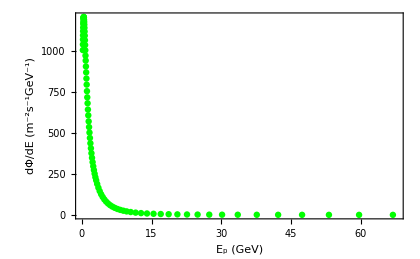

```mathematica
ListPlot[energyBins,FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Green,Thick]]
```

```mathematica
energyBins
```

{{0.206,1004.75},{0.218,1039},{0.231,1069.15},{0.244,1094.75},{0.259,1120},{0.274,1142},{0.29,1164.15},{0.307,1176.45},{0.326,1193.45},{0.345,1200.85},{0.366,1204.5},{0.387,1207.05},{0.41,1206.05},{0.435,1202.45},{0.46,1188.8},{0.487,1176.15},{0.516,1160.3},{0.547,1140.55},{0.579,1118.05},{0.614,1092.75},{0.65,1064.95},{0.688,1035.8},{0.729,1003.7},{0.772,971.1},{0.818,940.8},{0.866,905.05},{0.918,868.9},{0.972,831.4},{1.03,794.3},{1.091,754.35},{1.156,716.65},{1.224,680.6},{1.297,642.2},{1.374,606.95},{1.455,570.05},{1.541,535.55},{1.632,501.95},{1.729,468.9},{1.831,436.6},{1.94,406},{2.054,376.05},{2.176,347.95},{2.305,321.6},{2.442,296.25},{2.587,273.25},{2.74,250.95},{2.902,229.5},{3.074,210.55},{3.289,188.5},{3.551,165.7},{3.834,144.8},{4.14,126},{4.471,109.3},{4.827,94.38},{5.212,81.165},{5.628,69.605},{6.077,59.325},{6.562,50.475},{7.085,42.82},{7.65,36.1},{8.26,30.495},{8.919,25.505},{9.631,21.305},{10.505,17.395},{11.565,13.775},{12.73,10.91},{14.01,8.5975},{15.42,6.7365},{16.97,5.2745},{18.675,4.13},{20.555,3.209},{22.625,2.497},{24.905,1.9275},{27.415,1.4995},{30.175,1.157},{33.55,0.87225},{37.645,0.6363},{42.24,0.4644},{47.395,0.3392},{53.175,0.2481},{59.665,0.1807},{66.945,0.1315},{75.11,0.09677},{84.28,0.07018},{94.565,0.05062},{106.8,0.037575},{121.4,0.02622},{138,0.01871},{156.8,0.013255}}

```mathematica
intEB=Interpolation[energyBins,InterpolationOrder->1]
```

InterpolatingFunction[…]

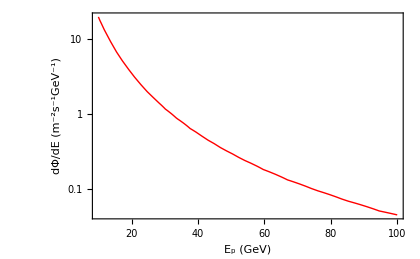

```mathematica
LogPlot[intEB[Ep],{Ep,10,100},FrameLabel->{"E_p (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```

## Pythia hadronization

First, we import the kaon results from our 10,000 event pythia runs.

```mathematica
For[i = 1, i <21, i++,  
If[i <10,
kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData0" <>ToString[i]<>".txt"}],"table"];
kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData0" <>ToString[i]<>".txt"}],"table"];kLPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kLPData0" <>ToString[i]<>".txt"}],"table"];
kLNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kLNData0" <>ToString[i]<>".txt"}],"table"],kaonPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kaonPData" <>ToString[i]<>".txt"}],"table"];kaonNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kaonNData" <>ToString[i]<>".txt"}],"table"];kLPData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","ProtonScatter","kLPData" <>ToString[i]<>".txt"}],"table"];
kLNData[i]=Import[FileNameJoin[{NotebookDirectory[],"Data","NeutronScatter","kLNData" <>ToString[i]<>".txt"}],"table"]
]

]
```

Test nested list element selection

```mathematica
kaonNData[1][[1]]
kaonNData[1][[1,3]]
kaonNData[1][[2]]
kLNData[2][[1]]
```

{Beams:eA,=,18.675}

18.675

{0,3.9598}

{Beams:eA,=,20.555}

Calculate number of kaons produced for a given energy bin

```mathematica
For[i = 1, i <21, i++,  
numPKaons[i]=Times@@Dimensions[kaonPData[i]]-1;
numNKaons[i]=Times@@Dimensions[kaonNData[i]]-1;
numPKLs[i]=Times@@Dimensions[kLPData[i]]-1;
numNKLs[i]=Times@@Dimensions[kLNData[i]]-1;
numKaons[i] = numNKaons[i]+numPKaons[i];
numKLs[i]=numNKLs[i]+numPKLs[i]
]
```

```mathematica
numPKaons[1];
numNKaons[1];
numKaons[2];
numNKLs[2];
numPKLs[2];
numKLs[2];
```

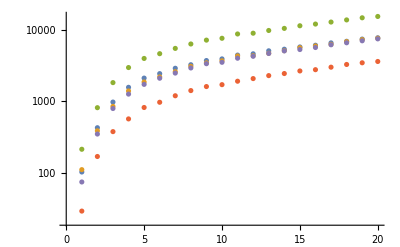

```mathematica
ListLogPlot[{Table[numPKaons[i],{i,1,20}],Table[numNKaons[i],{i,1,20}],Table[numKaons[i],{i,1,20}],Table[numPKLs[i],{i,1,20}],Table[numKLs[i],{i,1,20}]}]
```

Obtain a probability distribution of kaons over energy

### PDF Calculations

```mathematica
For[i = 1, i <21, i++,  
kEngPointsP=Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}];
smoothkEngP =SmoothKernelDistribution[kEngPointsP];
smoothkEng2P =SmoothKernelDistribution[Flatten@kEngPointsP,0.5];
trunkEngP[i] =TruncatedDistribution[{0,1000},smoothkEngP];
trunkEng2P[i] =TruncatedDistribution[{0,1000},smoothkEng2P];
]
For[i = 1, i <21, i++,  
kLEngPointsP=Table[kLPData[i][[j,2]],{j,2,numPKLs[i]+1}];
smoothkLEngP =SmoothKernelDistribution[kLEngPointsP];
smoothkLEng2P =SmoothKernelDistribution[Flatten@kLEngPointsP,0.5];
trunkLEngP[i] =TruncatedDistribution[{0,1000},smoothkLEngP];
trunkLEng2P[i] =TruncatedDistribution[{0,1000},smoothkLEng2P];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPointsN=Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}];
smoothkEngN =SmoothKernelDistribution[kEngPointsN];
smoothkEng2N =SmoothKernelDistribution[Flatten@kEngPointsN,0.5];
trunkEngN[i] =TruncatedDistribution[{0,1000},smoothkEngN];
trunkEng2N[i] =TruncatedDistribution[{0,1000},smoothkEng2N];
]
For[i = 1, i <21, i++,  
kLEngPointsN=Table[kLNData[i][[j,2]],{j,2,numNKLs[i]+1}];
smoothkLEngN =SmoothKernelDistribution[kLEngPointsN];
smoothkLEng2N =SmoothKernelDistribution[Flatten@kLEngPointsN,0.5];
trunkLEngN[i] =TruncatedDistribution[{0,1000},smoothkLEngN];
trunkLEng2N[i] =TruncatedDistribution[{0,1000},smoothkLEng2N];
]
```

```mathematica
For[i = 1, i <21, i++,  
kEngPoints=Join[Table[kaonNData[i][[j,2]],{j,2,numNKaons[i]+1}],Table[kaonPData[i][[j,2]],{j,2,numPKaons[i]+1}]];
smoothkEng =SmoothKernelDistribution[kEngPoints];
smoothkEng2 =SmoothKernelDistribution[Flatten@kEngPoints,0.5];
trunkEng[i] =TruncatedDistribution[{0,1000},smoothkEng];
trunkEng2[i] =TruncatedDistribution[{0,1000},smoothkEng2];
]
For[i = 1, i <21, i++,  
kLEngPoints=Join[Table[kLNData[i][[j,2]],{j,2,numNKLs[i]+1}],Table[kLPData[i][[j,2]],{j,2,numPKLs[i]+1}]];
smoothkLEng =SmoothKernelDistribution[kLEngPoints];
smoothkLEng2 =SmoothKernelDistribution[Flatten@kLEngPoints,0.5];
trunkLEng[i] =TruncatedDistribution[{0,1000},smoothkLEng];
trunkLEng2[i] =TruncatedDistribution[{0,1000},smoothkLEng2];
]
```

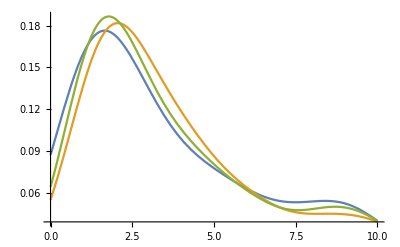

```mathematica
Plot[{PDF[trunkEngP[1],x],PDF[trunkEngN[1],x],PDF[trunkEng[1],x]},{x,0,10}]
```

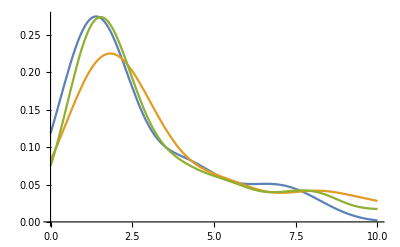

```mathematica
Plot[{PDF[trunkLEngP[1],x],PDF[trunkLEngN[1],x],PDF[trunkLEng[1],x]},{x,0,10}]
```

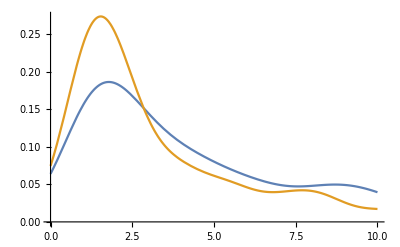

```mathematica
Plot[{PDF[trunkEng[1],x],PDF[trunkLEng[1],x]},{x,0,10}]
```

## LLP flux calculation

The overall form of this expression is: kaon energy distribution X kaons produced per proton X proton flux in a given energy bin

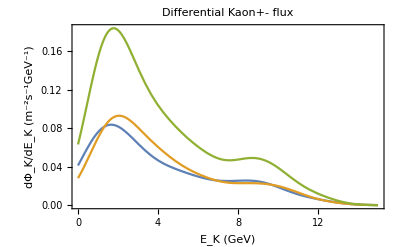

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkEngP[1],x]]*numPKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEngN[1],x]]*numNKaons[1]/(2*10^4)*( intEB[
kaonNData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon+- flux"]
```

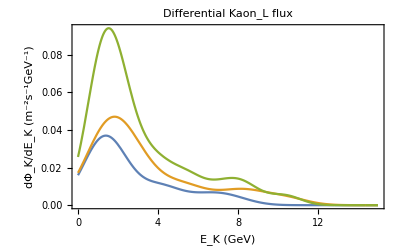

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkLEngP[1],x]]*numPKLs[1]/(2*10^4)*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkLEngN[1],x]]*numNKLs[1]/(2*10^4)*( intEB[
kLNData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Differential Kaon_L flux"]
```

Combined these! Note: for the purposes of obtaining phi decays (which have a BR 3.5 times higher for K_long than K+-) we can multiply the number of K longs by 3.5 and use the BR of the K+ to determine the phi distribution.

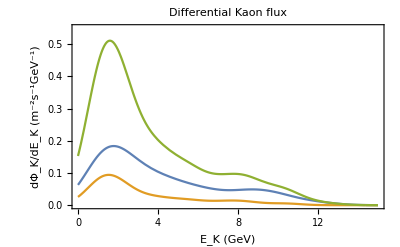

```mathematica
Plot[{4Pi*Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4)*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]),4Pi*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]]),4Pi*(3.5*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)+Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4))*( intEB[
kLPData[1][[1,3]]]* energyWidth[[1]])},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotRange-> {0,0.55},PlotLabel->"Differential Kaon flux"]
```

1st line is just one low energy (18 GeV) trial bin, the 2nd is all protons under 30 GeV, the 3rd is all under 50 GeV, the 4th is under 100 GeV, and the final is all energies that the data I’m using has information for. dKFluxPlot assumes an identical BR for both K long and K+ (used in the BR = 1 plot).

```mathematica
dKFlux18GeV=4Pi*(3.5*Evaluate[PDF[trunkLEng[1],x]]*numKLs[1]/(2*10^4)+Evaluate[PDF[trunkEng[1],x]]*numKaons[1]/(2*10^4))*( intEB[
kaonPData[1][[1,3]]]* energyWidth[[1]]);
dKFluxSub30=4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,5}];
dKFluxSub50 = 4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,10}];
dKFluxSub100 =4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,16}];
dKFluxAll =4Pi*Sum[(3.5*Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}];
dKFluxPlot=4Pi*Sum[(Evaluate[PDF[trunkLEng[i],x]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],x]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}];
```

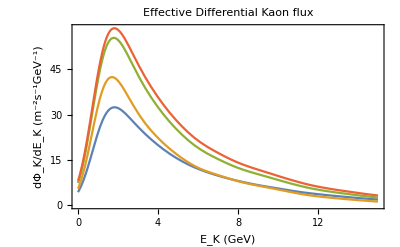

```mathematica
Plot[{(*dKFlux18GeV,dKFluxSub30*)dKFluxPlot,dKFluxSub50,dKFluxSub100,dKFluxAll},{x,0,15},Frame->True,FrameLabel->{"E_K (GeV)","dΦ_K/dE_K (m^-2s^-1GeV^-1)"},PlotLabel->"Effective Differential Kaon flux"]
```

## Geometry

Here, I introduce all the equations required for the geometry calculations including detector parameters.

```mathematica
L[θ_,R_,h_]:=R*Cos[θ]+Sqrt[h^2 + 2R*h+R^2 *Cos[θ]^2](*In km*)
G[R_,h_]:=N[Integrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))],{θ,0,Pi}]]
```

```mathematica
volSK=Pi*(14.9)^2*32.2; (*In m^3*)
volHK=8*volSK;
```

```mathematica
detectionTime = 365.25*10*24*3600; (*In s, assuming 10 year detection period*)
```

```mathematica
Gmod[R_,h_,phiEng_,mPhi_]:=NIntegrate[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))*Exp[-(L[θ,R,h]*1000)/disTravel[phiEng,mPhi]]],{θ,0,Pi}](*This includes the exponential part of the number of events integral*)
```

```mathematica
pointList = Import["llpLifetimePoints.csv"];
pointTable = Table[{pointList[[i,1]],pointList[[i,2]]},{i,1,Length[pointList]}];
intLT = Interpolation[pointTable,InterpolationOrder->1]
```

InterpolatingFunction[…]

## Maybe Run

## Scalar Kinematics

```mathematica
pPhiCM[mPhi_] :=Sqrt[(mKaon^2 -(mPi + mPhi)^2)(mKaon^2 -(mPi - mPhi)^2)]/(2*mKaon);
ePhiCM[mPhi_] := Sqrt[pPhiCM[mPhi]^2 + mPhi^2];
ePhi[mPhi_,eK_,ctheta_] :=(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]ctheta) ;
```

```mathematica
mKaon = 0.4937 ;(*In GeV*)
mPi = 0.1396 ;(*In GeV*)
me =0.000511;
ms=0.101;
mt=173;
md = 0.005;
CKMfactor = 3.6*10^(-4);
tauK = 1.24*10^(-8)*(1.5192675*10^(24));
```

Set ϕ mass and other inputs:

```mathematica
minEng = 1;(*GeV*)
step=0.15; (*GeV*)
mPhi = 0.150; (*In GeV*)
If[mPhi ≤ 0.2,tauPhiPlot = 10^(-1.116*Log[10,mPhi]+0.4777), tauPhiPlot = intLT[mPhi]];(*In s, from scalar spectator plot*)
mixingAngle = 5*10^(-4);
tauPhi = tauPhiPlot(10^(-6)/mixingAngle)^2;
minPhiEng = 0.05+ mPhi; (*Adjust these for final integral over Ephi: must be larger than mPhi*)
engStep = 0.1;
```

Calculate ϕ branching ratio:

```mathematica
Fkpi = ((mKaon^2 -mPi^2)/(ms -md))*fkpi;
fkpi =0.96(1+0.02(mPhi^2)/mPi^2);
```

```mathematica
phiBRWrong= 9*Sqrt[2]*tauK*mixingAngle^2 *Gf^3*mt^4*ms^2*CKMfactor^2*Fkpi^2pPhiCM[mPhi]/(512*Pi^5*mKaon^2)(*THIS IS WRONG!!! BR to scalar, from Arxiv:1312.2547. Note that I pulled in a 1/2mk into the pPhiCM*)
phiBR = 9*tauK*mixingAngle^2 *Gf^3*mt^4*mKaon^2*CKMfactor^2*pPhiCM[mPhi]/(2048*Sqrt[2]*Pi^5)(*Yue fixed*)
phiBR2 =Sin[mixingAngle]^2 *0.002*2pPhiCM[mPhi]/mKaon (*from Arxiv:1310.8042*)
phiBR3 = 1; (*Used to construct the plot for seeing the energy distribution of both kaons and phis*)
```

3.10326×10^-9

4.2918×10^-10

4.04852×10^-10

Define kinematic functions:

```mathematica
gamma[phiEng_,mPhi_] :=phiEng/mPhi (*phiEng in GeV*)
velPhi[phiEng_,mPhi_] := Sqrt[1-(1/gamma[phiEng,mPhi]^2 )]*c(*outputs m/s^2*)
disTravel[phiEng_,mPhi_]:=gamma[phiEng,mPhi]*velPhi[phiEng,mPhi]*tauPhi;(*output in m*)
```

Additional values for angular distribution plot

```mathematica
mPhi2 = 0.200; (*In GeV*)
If[mPhi2 ≤ 0.2,tauPhiPlot2 = 10^(-1.116*Log[10,mPhi2]+0.4777), tauPhiPlot2 = intLT[mPhi2]];
mixingAngle2=10^(-4);
tauPhi2=tauPhiPlot2(10^(-6)/mixingAngle2)^2
disTravel2[phiEng_,mPhi_]:=gamma[phiEng,mPhi]*velPhi[phiEng,mPhi]*tauPhi2;
mPhi3 = 0.010; (*In GeV*)
If[mPhi3 ≤ 0.2,tauPhiPlot3 = 10^(-1.116*Log[10,mPhi3]+0.4777), tauPhiPlot3 = intLT[mPhi3]];
mixingAngle3=10^(-2);
tauPhi3=tauPhiPlot3(10^(-6)/mixingAngle3)^2
disTravel3[phiEng_,mPhi_]:=gamma[phiEng,mPhi]*velPhi[phiEng,mPhi]*tauPhi3;
```

0.0018103

5.12507×10^-6

#### Create total probability distribution

```mathematica
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
ePhiDist= UniformDistribution[{(eK/mKaon)(ePhiCM[mPhi]-pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]),(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)])}];
truncEPhi[s] =TruncatedDistribution[{0,1000},ePhiDist];
]
```

```mathematica
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
x =minEng + (s-1)(step);
If[s == 1,totDist = truncEPhi[s],
t = 1;
fluxBelow = 0;
While[t< s,
x=minEng + (t-1)(step);
fluxBelow += dKFluxAll;
t++;
];
x=minEng + (s-1)(step);
fluxAt =dKFluxAll;
totDist=MixtureDistribution[{fluxBelow,fluxAt},{totDist,truncEPhi[s]}]  ]
]
```

```mathematica
totFlux = 0;
For[s = 1, s< (15/step), s++,
x =minEng + (s-1)(step);
totFlux +=dKFluxAll*step;
]
totFlux
```

297.419

#### Create probability distribution for BR = 1 plot (K_L and K_± have equal BR rather than different ones!).

```mathematica
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
ePhiDist2= UniformDistribution[{(eK/mKaon)(ePhiCM[mPhi]-pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)]),(eK/mKaon)(ePhiCM[mPhi]+pPhiCM[mPhi]Sqrt[1 - (mKaon^2)/(eK^2)])}];
truncEPhi2[s] =TruncatedDistribution[{0,1000},ePhiDist2];
]
```

```mathematica
For[s = 1, s< (15/step), s++,
eK =minEng + (s-1)(step);
x =minEng + (s-1)(step);
If[s == 1,totDist2 = truncEPhi2[s],
t = 1;
fluxBelow = 0;
While[t< s,
x=minEng + (t-1)(step);
fluxBelow += dKFluxPlot;
t++;
];
x=minEng + (s-1)(step);
fluxAt =dKFluxPlot;
totDist2=MixtureDistribution[{fluxBelow,fluxAt},{totDist2,truncEPhi2[s]}]  ]
]
```

```mathematica
totFlux2 = 0;
For[s = 1, s< (15/step), s++,
x =minEng + (s-1)(step);
totFlux2 +=dKFluxPlot*step;
]
totFlux2
```

166.646

## Number of Events

```mathematica
NumberOfEvents=Floor[volHK*detectionTime*Sum[engStep*Gmod[6400,10,minPhiEng + i*engStep,mPhi]*phiBR*PDF[totDist,minPhiEng+i*engStep]*totFlux/disTravel[minPhiEng+i*engStep,mPhi],{i,1,149}]]
```

68

## Plots

### Differential Flux

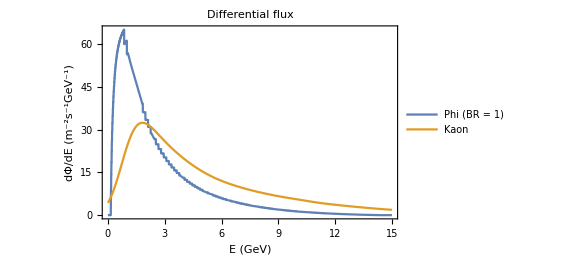

```mathematica
Plot[{PDF[totDist2,x]*totFlux2,dKFluxPlot},{x,0,15},Frame->True,LabelStyle->{Black,15},ImageSize->420,FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},PlotLabel->"Differential flux",PlotLegends-> {"Phi (BR = 1)","Kaon"}]
```

Need to fix the artifacts present from the pdf stitching!

```mathematica
numPts =75;
distTable = Table[{If[i==-1, 0,If[i==0,mPhi,N[i*15/numPts]]],If[i==-1,0,If[i==0, 0,totFlux2*PDF[totDist2,N[(i*15/numPts)]]]]},{i,-1,numPts}]
```

{{0,0},{0.15,0},{0.2,22.4285},{0.4,51.6639},{0.6,60.7685},{0.8,64.4087},{1.,61.2357},{1.2,53.1094},{1.4,49.5067},{1.6,42.3798},{1.8,39.1109},{2.,33.4246},{2.2,30.9683},{2.4,26.7172},{2.6,24.878},{2.8,23.2024},{3.,20.2716},{3.2,18.9864},{3.4,16.7159},{3.6,15.7112},{3.8,13.9233},{4.,13.1269},{4.2,11.7007},{4.4,11.0612},{4.6,9.90824},{4.8,9.38782},{5.,8.90062},{5.2,8.01485},{5.4,7.61133},{5.6,6.87227},{5.8,6.53318},{6.,5.90855},{6.2,5.62059},{6.4,5.08818},{6.6,4.84191},{6.8,4.3851},{7.,4.17308},{7.2,3.77856},{7.4,3.59493},{7.6,3.41973},{7.8,3.09292},{8.,2.94048},{8.2,2.65554},{8.4,2.52228},{8.6,2.27248},{8.8,2.1554},{9.,1.93579},{9.2,1.83295},{9.4,1.64064},{9.6,1.55095},{9.8,1.38379},{10.,1.30597},{10.2,1.16077},{10.4,1.09296},{10.6,1.02807},{10.8,0.906334},{11.,0.849199},{11.2,0.741843},{11.4,0.691451},{11.6,0.596873},{11.8,0.552548},{12.,0.469482},{12.2,0.430616},{12.4,0.357929},{12.6,0.323999},{12.8,0.260674},{13.,0.231146},{13.2,0.202952},{13.4,0.150318},{13.6,0.125771},{13.8,0.0799767},{14.,0.0586244},{14.2,0.0187028},{14.4,0.},{14.6,0.},{14.8,0.},{15.,0.}}

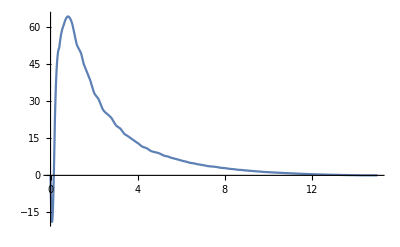

```mathematica
intDistTable=Interpolation[distTable,InterpolationOrder->3];
Plot[intDistTable[x],{x,0,15}]
```

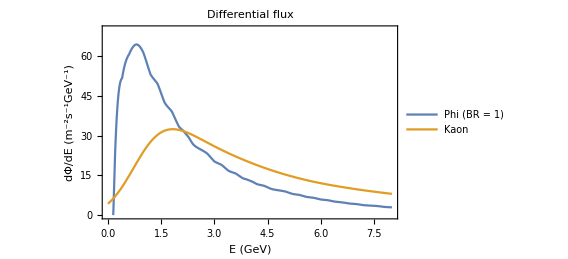

```mathematica
Plot[{intDistTable[x],dKFluxPlot},{x,0,8},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotRange -> {0,70},FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"},PlotLabel->"Differential flux",PlotLegends-> Placed[{"Phi (BR = 1)","Kaon"},{0.65,0.8}]]
```

### Convert To Histograms

```mathematica
testpts = 1000;
divisions = 80;
```

```mathematica
Clear[KaonMCHits]
TotalTests = testpts*divisions
KaonMCHits= ConstantArray[0,TotalTests/testpts];
divisionsList = ConstantArray[0,divisions];
Clear[PhiMCHits]
PhiMCHits= ConstantArray[0,TotalTests/testpts];
```

80000

```mathematica
For[k=1,k≤divisions,k++,
KaonMCDist=RandomReal[{0,1},{testpts,2}];
For[j=1,j≤testpts,j++,
n=KaonMCDist[[j,1]]*(8/divisions)+k*(8/divisions);
If[KaonMCDist[[j,2]]*40<4Pi*Sum[(Evaluate[PDF[trunkLEng[i],n]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],n]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}],KaonMCHits[[k]]++;divisionsList[[k]]=(k+0.5)*(8/divisions)
(*Print[KaonMCDist[[j,2]]*40," ",4Pi*Sum[(Evaluate[PDF[trunkLEng[i],n]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],n]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}]," yes"]*)
]
]
]
KaonMCHits
```

{160,199,259,287,339,401,458,490,579,614,677,712,739,773,776,802,827,807,801,812,810,778,765,735,718,709,683,675,639,645,624,622,600,552,534,540,531,512,496,488,470,455,493,448,423,388,388,387,420,356,364,371,366,323,344,328,294,339,295,280,302,278,303,264,251,264,248,248,245,264,233,197,229,199,232,224,221,202,200,189}

```mathematica
For[k=1,k≤divisions,k++,
PhiMCDist=RandomReal[{0,1},{testpts,2}];
For[j=1,j≤testpts,j++,
n=PhiMCDist[[j,1]]*(8/divisions)+k*(8/divisions);
If[PhiMCDist[[j,2]]*70<intDistTable[n],PhiMCHits[[k]]++
(*Print[KaonMCDist[[j,2]]*40," ",4Pi*Sum[(Evaluate[PDF[trunkLEng[i],n]]*numKLs[i]/(2*10^4)+Evaluate[PDF[trunkEng[i],n]]*numKaons[i]/(2*10^4))*( intEB[
kaonPData[i][[1,3]]]* energyWidth[[i]]),{i,1,20}]," yes"]*)
]
]
]
PhiMCHits
```

{68,501,722,779,857,885,910,918,872,852,787,719,726,679,621,609,559,540,503,488,455,442,374,369,339,346,350,332,305,289,294,259,256,226,235,219,189,204,198,186,182,155,155,158,152,145,142,131,125,113,95,97,92,107,103,99,97,85,92,94,84,98,81,73,64,58,71,61,53,60,42,42,41,51,43,48,52,34,40,45}

```mathematica
val=divisionsList;
freq=KaonMCHits;
l=Length[val];
w=8/divisions;(*bin width*)
data=Flatten@Array[Table[val[[#]],{freq[[#]]}]&,l];
freq2=PhiMCHits;
data2=Flatten@Array[Table[val[[#]],{freq2[[#]]}]&,l];
```

```mathematica
ClearAll[ceF]
ceF[sc_:1][cedf_:"Rectangle",o:OptionsPattern[]]:=Module[{origin=Charting`ChartStyleInformation["BarOrigin"],box=#},Switch[origin,Bottom,box[[2,2]]=sc box[[2,2]],Top,box[[2,1]]=sc box[[2,1]],Left,box[[1,2]]=sc box[[1,2]],Right,box[[1,1]]=sc box[[1,1]]];
ChartElementDataFunction[cedf,o][box,##2]]&;
```

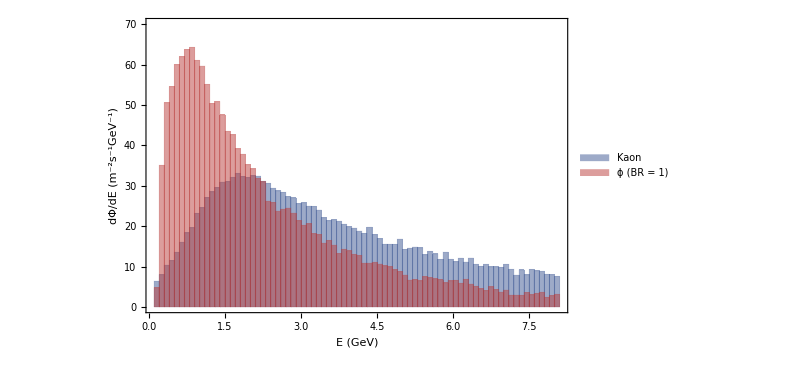

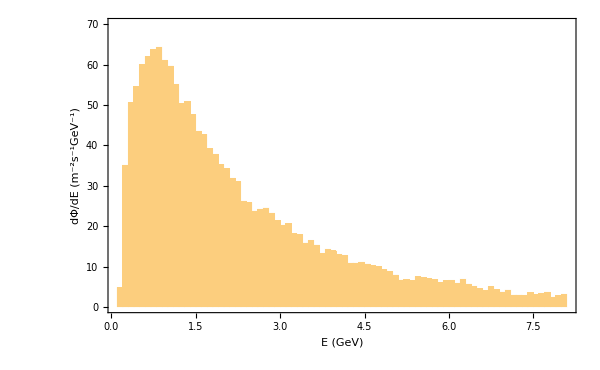

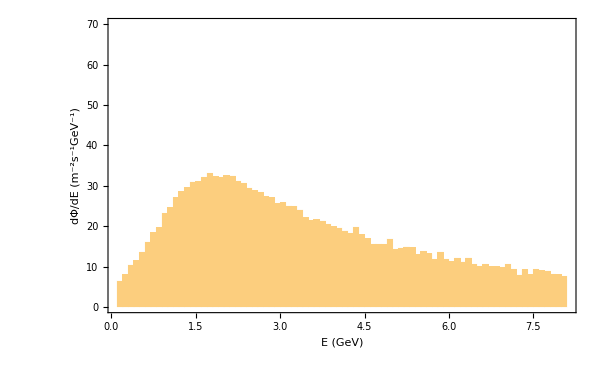

```mathematica
Histogram[{data,data2},{w},ChartElementFunction->{ceF[40/testpts][],ceF[70/testpts][]},ChartLegends-> Placed[{"Kaon","ϕ (BR = 1)"},{{0.85,0.8}}] ,ChartStyle->"DarkRainbow",Frame->True,LabelStyle->{Black,15},ImageSize->600,PlotRange -> {0,70},FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"}]
Histogram[data2,{w},70/testpts #2&,Frame->True,LabelStyle->{Black,15},ImageSize->600,PlotRange -> {0,70},FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"}]
Histogram[data,{w},40/testpts #2&,Frame->True,LabelStyle->{Black,15},ImageSize->600,PlotRange -> {0,70},FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"}]
```

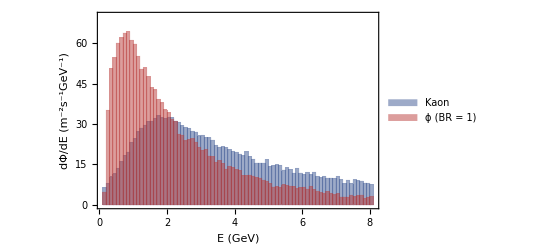

```mathematica
Histogram[{data,data2},{w},ChartElementFunction->{ceF[40/testpts][],ceF[70/testpts][]},ChartLegends-> Placed[{"Kaon","ϕ (BR = 1)"},{{0.7,0.8}}] ,ChartStyle->"DarkRainbow",Frame->True,LabelStyle->{Black,14,FontFamily->"Times"},ImageSize->400,PlotRange -> {0,70},FrameLabel->{"E (GeV)","dΦ/dE (m^-2s^-1GeV^-1)"}]
```

### Theta Distribution

```mathematica
G2[R_,h_,θ_]:=N[Evaluate[Sin[θ]*((R+h)/L[θ,R,h])(1+((R*Cos[θ])/(L[θ,R,h]-R*Cos[θ])))]]
```

```mathematica
thetaDist[R_,h_,θ_,mPhi_]:=Sum[engStep*G2[R,h,θ]*Exp[-(L[θ,R,h]*1000)/(disTravel[minPhiEng + i*engStep,mPhi])]*PDF[totDist,minPhiEng+i*engStep]/disTravel[minPhiEng+i*engStep,mPhi],{i,1,149}]
```

```mathematica
thetaDist2[R_,h_,θ_,mPhi_]:=Sum[engStep*G2[R,h,θ]*Exp[-(L[θ,R,h]*1000)/(disTravel2[minPhiEng + i*engStep,mPhi])]*PDF[totDist,minPhiEng+i*engStep]/disTravel2[minPhiEng+i*engStep,mPhi],{i,1,149}]
thetaDist3[R_,h_,θ_,mPhi_]:=Sum[engStep*G2[R,h,θ]*Exp[-(L[θ,R,h]*1000)/(disTravel3[minPhiEng + i*engStep,mPhi])]*PDF[totDist,minPhiEng+i*engStep]/disTravel3[minPhiEng+i*engStep,mPhi],{i,1,149}]
```

```mathematica
thetaDist[6400,10,Pi/2.5,mPhi]
```

2.02836×10^-8

```mathematica
thetaNormalization = Sum[(Pi/100)*thetaDist[6400,10,i*Pi/100,mPhi],{i,40,100}]
```

9.5092×10^-6

```mathematica
thetaNormalization2 = Sum[(Pi/100)*thetaDist2[6400,10,i*Pi/100,mPhi2],{i,30,100}]
```

1.47629×10^-6

```mathematica
thetaNormalization3 = Sum[(Pi/100)*thetaDist3[6400,10,i*Pi/100,mPhi3],{i,40,100}]
```

0.0000109725

```mathematica
numPtsAngle =100;
angleDistTable = Table[{N[Cos[(i-1/2)*Pi/numPtsAngle]],If[(i-1/2)*Pi/numPtsAngle<1.4,0,thetaDist[6400,10,N[(i-1/2)*Pi/numPtsAngle],mPhi]/thetaNormalization]},{i,1,numPtsAngle}]
```

{{0.999877,0},{0.99889,0},{0.996917,0},{0.993961,0},{0.990024,0},{0.985109,0},{0.979223,0},{0.97237,0},{0.964557,0},{0.955793,0},{0.946085,0},{0.935444,0},{0.92388,0},{0.911403,0},{0.898028,0},{0.883766,0},{0.868632,0},{0.85264,0},{0.835807,0},{0.81815,0},{0.799685,0},{0.78043,0},{0.760406,0},{0.739631,0},{0.718126,0},{0.695913,0},{0.673013,0},{0.649448,0},{0.625243,0},{0.60042,0},{0.575005,0},{0.549023,0},{0.522499,0},{0.495459,0},{0.46793,0},{0.439939,0},{0.411514,0},{0.382683,0},{0.353475,0},{0.323917,0},{0.29404,0},{0.263873,0},{0.233445,0},{0.202787,0},{0.171929,0},{0.140901,0.0346041},{0.109734,0.069659},{0.0784591,0.155352},{0.0471065,0.386239},{0.0157073,0.971675},{-0.0157073,1.81136},{-0.0471065,2.19213},{-0.0784591,2.13747},{-0.109734,1.9489},{-0.140901,1.74852},{-0.171929,1.56832},{-0.202787,1.41316},{-0.233445,1.28074},{-0.263873,1.16741},{-0.29404,1.06973},{-0.323917,0.98481},{-0.353475,0.910352},{-0.382683,0.84452},{-0.411514,0.785857},{-0.439939,0.733202},{-0.46793,0.685621},{-0.495459,0.642358},{-0.522499,0.602793},{-0.549023,0.566419},{-0.575005,0.532812},{-0.60042,0.501618},{-0.625243,0.47254},{-0.649448,0.445325},{-0.673013,0.419757},{-0.695913,0.395651},{-0.718126,0.372846},{-0.739631,0.351203},{-0.760406,0.330601},{-0.78043,0.310932},{-0.799685,0.292103},{-0.81815,0.274029},{-0.835807,0.256637},{-0.85264,0.23986},{-0.868632,0.223637},{-0.883766,0.207915},{-0.898028,0.192644},{-0.911403,0.17778},{-0.92388,0.163281},{-0.935444,0.14911},{-0.946085,0.135232},{-0.955793,0.121614},{-0.964557,0.108225},{-0.97237,0.0950384},{-0.979223,0.0820256},{-0.985109,0.0691612},{-0.990024,0.0564206},{-0.993961,0.0437802},{-0.996917,0.0312169},{-0.99889,0.0187084},{-0.999877,0.00623251}}

```mathematica
angleDistTable2 = Table[{N[Cos[(i-1/2)*Pi/numPtsAngle]],If[(i-1/2)*Pi/numPtsAngle<1,0,thetaDist2[6400,10,N[(i-1/2)*Pi/numPtsAngle],mPhi2]/thetaNormalization2]},{i,1,numPtsAngle}]
```

{{0.999877,0},{0.99889,0},{0.996917,0},{0.993961,0},{0.990024,0},{0.985109,0},{0.979223,0},{0.97237,0},{0.964557,0},{0.955793,0},{0.946085,0},{0.935444,0},{0.92388,0},{0.911403,0},{0.898028,0},{0.883766,0},{0.868632,0},{0.85264,0},{0.835807,0},{0.81815,0},{0.799685,0},{0.78043,0},{0.760406,0},{0.739631,0},{0.718126,0},{0.695913,0},{0.673013,0},{0.649448,0},{0.625243,0},{0.60042,0},{0.575005,0},{0.549023,0},{0.522499,0.0408242},{0.495459,0.046895},{0.46793,0.0541875},{0.439939,0.0630293},{0.411514,0.0738613},{0.382683,0.0872869},{0.353475,0.104148},{0.323917,0.125646},{0.29404,0.153539},{0.263873,0.190476},{0.233445,0.240588},{0.202787,0.310571},{0.171929,0.411775},{0.140901,0.564404},{0.109734,0.806039},{0.0784591,1.20696},{0.0471065,1.87337},{0.0157073,2.74923},{-0.0157073,3.07585},{-0.0471065,2.59658},{-0.0784591,2.02962},{-0.109734,1.61113},{-0.140901,1.31803},{-0.171929,1.1077},{-0.202787,0.951279},{-0.233445,0.830992},{-0.263873,0.735803},{-0.29404,0.658634},{-0.323917,0.594786},{-0.353475,0.541038},{-0.382683,0.495117},{-0.411514,0.455374},{-0.439939,0.42059},{-0.46793,0.389843},{-0.495459,0.362423},{-0.522499,0.337776},{-0.549023,0.315464},{-0.575005,0.295132},{-0.60042,0.276496},{-0.625243,0.259321},{-0.649448,0.243413},{-0.673013,0.228609},{-0.695913,0.214772},{-0.718126,0.201787},{-0.739631,0.189554},{-0.760406,0.177988},{-0.78043,0.167016},{-0.799685,0.156574},{-0.81815,0.146604},{-0.835807,0.137058},{-0.85264,0.127892},{-0.868632,0.119066},{-0.883766,0.110547},{-0.898028,0.102301},{-0.911403,0.0943023},{-0.92388,0.0865237},{-0.935444,0.0789419},{-0.946085,0.0715355},{-0.955793,0.0642844},{-0.964557,0.0571701},{-0.97237,0.0501754},{-0.979223,0.0432838},{-0.985109,0.0364802},{-0.990024,0.0297496},{-0.993961,0.0230782},{-0.996917,0.0164523},{-0.99889,0.00985853},{-0.999877,0.00328405}}

```mathematica
angleDistTable3 = Table[{N[Cos[(i-1/2)*Pi/numPtsAngle]],If[(i-1/2)*Pi/numPtsAngle<1.4,0,thetaDist3[6400,10,N[(i-1/2)*Pi/numPtsAngle],mPhi3]/thetaNormalization3]},{i,1,numPtsAngle}]
```

{{0.999877,0},{0.99889,0},{0.996917,0},{0.993961,0},{0.990024,0},{0.985109,0},{0.979223,0},{0.97237,0},{0.964557,0},{0.955793,0},{0.946085,0},{0.935444,0},{0.92388,0},{0.911403,0},{0.898028,0},{0.883766,0},{0.868632,0},{0.85264,0},{0.835807,0},{0.81815,0},{0.799685,0},{0.78043,0},{0.760406,0},{0.739631,0},{0.718126,0},{0.695913,0},{0.673013,0},{0.649448,0},{0.625243,0},{0.60042,0},{0.575005,0},{0.549023,0},{0.522499,0},{0.495459,0},{0.46793,0},{0.439939,0},{0.411514,0},{0.382683,0},{0.353475,0},{0.323917,0},{0.29404,0},{0.263873,0},{0.233445,0},{0.202787,0},{0.171929,0},{0.140901,0.0209768},{0.109734,0.044713},{0.0784591,0.106164},{0.0471065,0.283359},{0.0157073,0.773203},{-0.0157073,1.56405},{-0.0471065,2.01398},{-0.0784591,2.04397},{-0.109734,1.91237},{-0.140901,1.74597},{-0.171929,1.58563},{-0.202787,1.44202},{-0.233445,1.31622},{-0.263873,1.20651},{-0.29404,1.11059},{-0.323917,1.02627},{-0.353475,0.951658},{-0.382683,0.88519},{-0.411514,0.825583},{-0.439939,0.77179},{-0.46793,0.72295},{-0.495459,0.678359},{-0.522499,0.637433},{-0.549023,0.599684},{-0.575005,0.564706},{-0.60042,0.532156},{-0.625243,0.501742},{-0.649448,0.473215},{-0.673013,0.446363},{-0.695913,0.421},{-0.718126,0.396968},{-0.739631,0.374126},{-0.760406,0.352352},{-0.78043,0.331538},{-0.799685,0.311589},{-0.81815,0.29242},{-0.835807,0.273955},{-0.85264,0.256127},{-0.868632,0.238873},{-0.883766,0.222138},{-0.898028,0.205872},{-0.911403,0.190029},{-0.92388,0.174566},{-0.935444,0.159445},{-0.946085,0.144628},{-0.955793,0.130083},{-0.964557,0.115777},{-0.97237,0.101681},{-0.979223,0.0877673},{-0.985109,0.0740086},{-0.990024,0.0603792},{-0.993961,0.0468544},{-0.996917,0.0334103},{-0.99889,0.0200234},{-0.999877,0.00667068}}

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

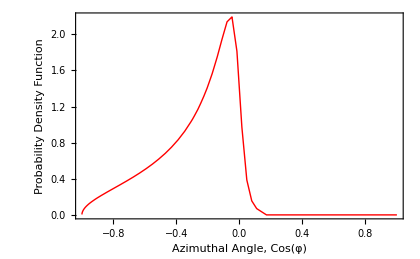

```mathematica
intAngDistTable=Interpolation[angleDistTable,InterpolationOrder->1];
Plot[intAngDistTable[x],{x,-1,1},Frame->True,LabelStyle->{Black,15},ImageSize->420,Axes-> False,FrameLabel->{"Azimuthal Angle, Cos(φ)","Probability Density Function"},PlotStyle->Directive[Red,Thick]]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

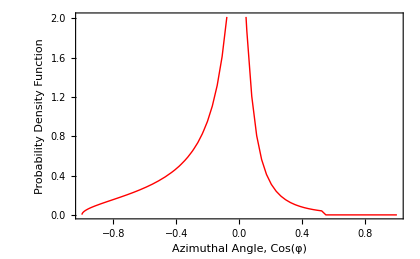

```mathematica
intAngDistTable2=Interpolation[angleDistTable2,InterpolationOrder->1];
Plot[intAngDistTable2[x],{x,-1,1},Frame->True,LabelStyle->{Black,15},ImageSize->420,Axes-> False,FrameLabel->{"Azimuthal Angle, Cos(φ)","Probability Density Function"},PlotStyle->Directive[Red,Thick]]
```

InterpolatingFunction::dmval: Input value {-0.999959} lies outside the range of data in the interpolating function. Extrapolation will be used.

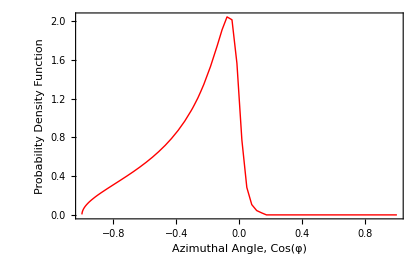

```mathematica
intAngDistTable3=Interpolation[angleDistTable3,InterpolationOrder->1];
Plot[intAngDistTable3[x],{x,-1,1},Frame->True,LabelStyle->{Black,15},ImageSize->420,Axes-> False,FrameLabel->{"Azimuthal Angle, Cos(φ)","Probability Density Function"},PlotStyle->Directive[Red,Thick]]
```

The version below is too slow to run every time I use the notebook!

```mathematica
(*Plot[thetaDist[6400,10,θ,mPhi]/thetaNormalization,{θ,0,Pi},Frame->True,LabelStyle->{Black,15},ImageSize->420,FrameLabel->{"Polar Angle (θ)","Probability Density Function"},PlotLabel->"Angular distribution of detectable ϕ",PlotStyle->Directive[Red,Thick]]*)
```

### Convert To Histograms

```mathematica
testpts = 1000;
divisions = 100;
```

```mathematica
Clear[AngleMCHits]
TotalTests = testpts*divisions
AngleMCHits= ConstantArray[0,TotalTests/testpts];
divisionsList = ConstantArray[0,divisions];
Clear[AngleMCHits2]
AngleMCHits2= ConstantArray[0,TotalTests/testpts];
```

100000

```mathematica
For[k=1,k≤divisions,k++,
AngleMCDist=RandomReal[{0,1},{testpts,2}];
divisionsList[[k]]=(k+0.5)*(2/divisions) - 1;
For[j=1,j≤testpts,j++,
n=AngleMCDist[[j,1]]*(2/divisions)+k*(2/divisions)-1;(*Gives cos(φ) for out trial*)
If[n>0.1,0,
If[AngleMCDist[[j,2]]*2.3< intAngDistTable[n],AngleMCHits[[k]]++(*normally where division list goes*)]
]
]
]
AngleMCHits
```

{31,36,77,78,92,101,104,105,126,129,139,134,154,165,174,195,189,214,234,208,258,266,262,280,266,319,320,360,319,344,386,415,425,449,483,500,538,585,618,653,679,744,789,839,877,950,943,855,742,515,295,163,78,58,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
For[k=1,k≤divisions,k++,
AngleMCDist2=RandomReal[{0,1},{testpts,2}];
For[j=1,j≤testpts,j++,
n=AngleMCDist2[[j,1]]*(2/divisions)+k*(2/divisions)-1;(*Gives cos(φ) for out trial*)
If[n>0.7,0,
If[AngleMCDist2[[j,2]]*2.8< intAngDistTable2[n],AngleMCHits2[[k]]++]
]
]
]
AngleMCHits2
```

{21,17,32,38,45,33,41,46,50,65,54,65,73,65,75,86,100,87,97,98,111,117,117,126,132,135,141,170,174,171,182,194,198,222,234,270,256,295,315,366,413,448,504,581,657,778,917,995,1000,991,849,649,512,375,271,243,185,168,142,102,67,87,68,48,50,31,31,32,24,31,25,27,14,16,11,10,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
val=divisionsList;
freq=AngleMCHits;
l=Length[val];
w=2/divisions;(*bin width*)
data=Flatten@Array[Table[val[[#]],{freq[[#]]}]&,l];
freq2=AngleMCHits2;
data2=Flatten@Array[Table[val[[#]],{freq2[[#]]}]&,l];
```

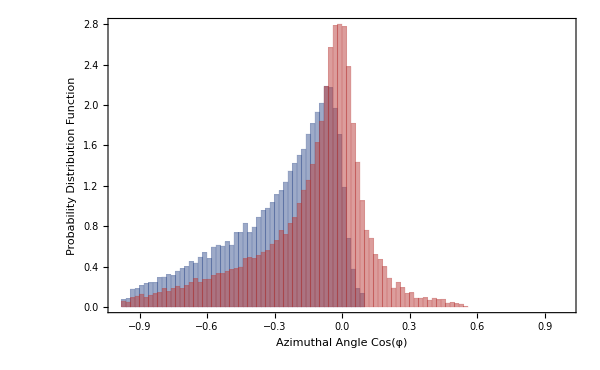

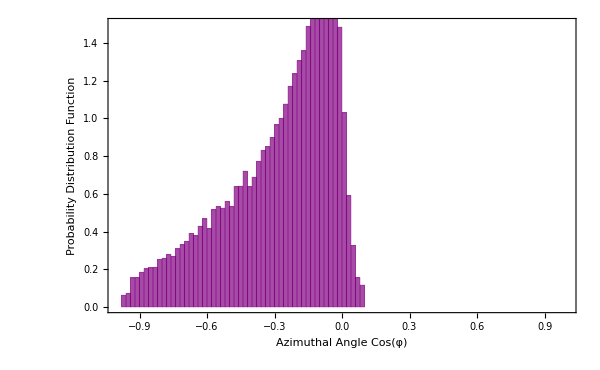

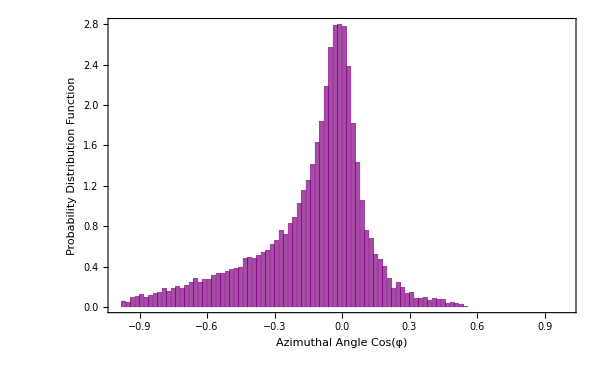

```mathematica
Histogram[{data,data2},{w},ChartElementFunction->{ceF[2.3/testpts][],ceF[2.8/testpts][]} ,ChartStyle->"DarkRainbow",Frame-> True,ImageSize->600,PlotRange ->{{-1,1},{0,2.8}},FrameLabel->{"Azimuthal Angle Cos(φ)","Probability Distribution Function"}]
Histogram[data,{w},2/testpts #2&,Frame->True,LabelStyle->{Black,15},ChartStyle->Opacity[.7,Purple],ImageSize->600,PlotRange ->{{-1,1},{0,1.5}},FrameLabel->{"Azimuthal Angle Cos(φ)","Probability Distribution Function"}]
Histogram[data2,{w},2.8/testpts #2&,Frame->True,LabelStyle->{Black,15},ChartStyle->Opacity[.7,Purple],ImageSize->600,PlotRange ->{{-1,1},{0,2.8}},FrameLabel->{"Azimuthal Angle Cos(φ)","Probability Distribution Function"}]
```

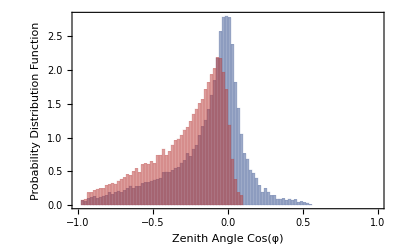

```mathematica
Histogram[{data2,data},{w},ChartElementFunction->{ceF[2.8/testpts][],ceF[2.3/testpts][]} ,ChartStyle->"DarkRainbow",Frame-> True,LabelStyle->{Black,14,FontFamily->"Times"},ImageSize->400,PlotRange ->{{-1,1},{0,2.8}},FrameLabel->{"Zenith Angle Cos(φ)","Probability Distribution Function"}]
```

### Opening Angle

```mathematica
pe[mPhi_] := (mPhi/2) Sqrt[1-(2*me/mPhi)^2]
```

```mathematica
Ee[mPhi_] :=Sqrt[pe[mPhi]^2 + me^2]
```

```mathematica
minPhiEng2 = 0.16;
```

```mathematica
OpeningAngle[phiEng_,mPhi_] := ArcTan[(0.866)pe[mPhi]*c/(Abs[gamma[phiEng,mPhi]*pe[mPhi]*(1/2)-velPhi[phiEng,mPhi]*gamma[phiEng,mPhi]*Ee[mPhi]])]*180/Pi+ArcTan[(0.866)pe[mPhi]*c/(Abs[gamma[phiEng,mPhi]*pe[mPhi]*(1/2)+velPhi[phiEng,mPhi]*gamma[phiEng,mPhi]*Ee[mPhi]])]*180/Pi
```

```mathematica
OADistNorm[mPhi_]:=(180/Pi)Sum[engStep/10*Gmod[6400,10,minPhiEng2 + i*engStep/10,mPhi]*PDF[totDist,minPhiEng2+i*engStep/10]/disTravel[minPhiEng2+i*engStep/10,mPhi],{i,1,1490}]
```

```mathematica
OpeningAngle[0.16,0.15]
```

133.597

```mathematica
(Gmod[6400,10,0.16,mPhi]*PDF[totDist,0.16]/disTravel[0.16,mPhi])/OADNorm
```

(7.32857×10^-7)/OADNorm

```mathematica
OADNorm =OADistNorm[mPhi]
```

0.000563522

```mathematica
OADistList[mPhi_] := Table[{OpeningAngle[minPhiEng2+i*engStep/10,mPhi],If[OpeningAngle[minPhiEng2+i*engStep/10,mPhi]<0.1,0,(Gmod[6400,10,minPhiEng2 + i*engStep/10,mPhi]*PDF[totDist,minPhiEng2+i*engStep/10]/disTravel[minPhiEng2+i*engStep/10,mPhi])/OADNorm]},{i,0,1490}]
```

```mathematica
OADistList[0.150]
```

{{133.597,0.00130049},{116.744,0.0029014},{105.097,0.0043654},{96.1662,0.00566832},{88.9552,0.00681388},{82.9429,0.00781179},{77.8168,0.00867421},{73.373,0.00854776},{69.4701,0.00927021},{66.0062,0.00988823},{62.905,0.0104138},{60.108,0.0102502},{57.5693,0.0106891},{55.2524,0.0110592},{53.1277,0.0108912},{51.1708,0.0111997},{49.3616,0.0114577},{47.683,0.0112921},{46.1209,0.0115064},{44.6628,0.0116839},{43.2984,0.0118295},{42.0184,0.0116701},{40.8151,0.0117893},{39.6814,0.0118848},{38.6113,0.0117329},{37.5995,0.0118094},{36.641,0.0118679},{35.7318,0.0117237},{34.8679,0.0117683},{34.046,0.0117991},{33.2631,0.0116626},{32.5163,0.0116832},{31.8031,0.0116932},{31.1213,0.0115641},{30.4687,0.0115667},{29.8436,0.0115611},{29.2442,0.0114391},{28.6688,0.0114281},{28.1161,0.0114107},{27.5847,0.0112952},{27.0734,0.011274},{26.5811,0.0112478},{26.1066,0.0111385},{25.649,0.0111096},{25.2075,0.011077},{24.7811,0.0109735},{24.3692,0.0109392},{23.9709,0.0109021},{23.5856,0.010804},{23.2126,0.0107659},{22.8514,0.0107257},{22.5014,0.0106326},{22.1622,0.0105919},{21.8331,0.0105496},{21.5137,0.0104612},{21.2037,0.0104188},{20.9026,0.0103751},{20.61,0.0102909},{20.3256,0.0102473},{20.0489,0.0102027},{19.7798,0.0101226},{19.5179,0.0100782},{19.2629,0.0100331},{19.0145,0.00995668},{18.7726,0.00991193},{18.5367,0.00986659},{18.3068,0.00979372},{18.0825,0.00974895},{17.8637,0.00970378},{17.6502,0.00963417},{17.4417,0.00883146},{17.2382,0.00879204},{17.0394,0.00873074},{16.8452,0.00869188},{16.6553,0.00865278},{16.4698,0.00859408},{16.2883,0.00855557},{16.1108,0.00851689},{15.9372,0.00846063},{15.7673,0.00842255},{15.601,0.00838433},{15.4382,0.00833037},{15.2788,0.00829275},{15.1227,0.00825503},{14.9697,0.00820322},{14.8198,0.00752427},{14.6729,0.00749101},{14.5289,0.00744514},{14.3877,0.00741234},{14.2493,0.00737944},{14.1135,0.00733532},{13.9803,0.00730288},{13.8496,0.00727039},{13.7213,0.00722792},{13.5954,0.0071959},{13.4717,0.00716385},{13.3504,0.00712294},{13.2312,0.00709137},{13.1141,0.00705981},{12.999,0.00646691},{12.886,0.00643891},{12.775,0.0064109},{12.6658,0.00637587},{12.5585,0.00634829},{12.4531,0.00632075},{12.3493,0.00628694},{12.2473,0.00625984},{12.147,0.00622681},{12.0483,0.00620015},{11.9512,0.00617356},{11.8557,0.00614165},{11.7617,0.0061155},{11.6692,0.00608944},{11.5781,0.00557971},{11.4884,0.0055565},{11.4001,0.00553336},{11.3132,0.00550587},{11.2276,0.00548311},{11.1433,0.00546043},{11.0602,0.00543382},{10.9784,0.00541151},{10.8978,0.00538929},{10.8183,0.00536351},{10.74,0.00534164},{10.6629,0.00531986},{10.5868,0.00529488},{10.5119,0.00527345},{10.4379,0.00483779},{10.3651,0.00481548},{10.2932,0.00479636},{10.2223,0.00477731},{10.1524,0.00475566},{10.0834,0.0047369},{10.0154,0.00471821},{9.94832,0.00469721},{9.88211,0.00467881},{9.81678,0.00466049},{9.7523,0.00464009},{9.68867,0.00462205},{9.62587,0.00460409},{9.56388,0.00458427},{9.50268,0.00420855},{9.44226,0.00419249},{9.38261,0.00417474},{9.32371,0.00415892},{9.26555,0.0041415},{9.2081,0.00412425},{9.15137,0.00410716},{9.09534,0.00409023},{9.03998,0.00407346},{8.9853,0.00405685},{8.93128,0.00404039},{8.8779,0.00402408},{8.82516,0.00400792},{8.77304,0.00399191},{8.72154,0.00366688},{8.67064,0.00365238},{8.62033,0.00363801},{8.5706,0.00362377},{8.52145,0.00360965},{8.47285,0.00359566},{8.42481,0.0035818},{8.37731,0.00356805},{8.33034,0.00355443},{8.2839,0.00354092},{8.23798,0.00352753},{8.19256,0.00351425},{8.14764,0.00350109},{8.10321,0.00348797},{8.05926,0.00320818},{8.01579,0.00319633},{7.97279,0.00318458},{7.93024,0.00317293},{7.88815,0.00316138},{7.8465,0.00314992},{7.8053,0.00313856},{7.76452,0.00312729},{7.72417,0.00311611},{7.68423,0.00310502},{7.64471,0.00309402},{7.60559,0.00308311},{7.56687,0.00307229},{7.52854,0.00306155},{7.4906,0.0028203},{7.45304,0.00281053},{7.41586,0.00280084},{7.37905,0.00279122},{7.3426,0.00278167},{7.3065,0.0027722},{7.27077,0.00276281},{7.23538,0.00275348},{7.20033,0.00274423},{7.16562,0.00273505},{7.13125,0.00272593},{7.0972,0.00271689},{7.06348,0.00270791},{7.03008,0.00249882},{6.99699,0.00249063},{6.96422,0.0024825},{6.93175,0.00247444},{6.89958,0.00246643},{6.8677,0.00245848},{6.83613,0.00245059},{6.80484,0.00244275},{6.77383,0.00243497},{6.74311,0.00242725},{6.71267,0.00241958},{6.6825,0.00241197},{6.6526,0.00240441},{6.62297,0.00239691},{6.5936,0.00221587},{6.56448,0.00220901},{6.53563,0.00220219},{6.50703,0.00219543},{6.47868,0.00218871},{6.45057,0.00218203},{6.42271,0.00217541},{6.39509,0.00216882},{6.3677,0.00216229},{6.34055,0.00215579},{6.31363,0.00214935},{6.28693,0.00214294},{6.26047,0.00213658},{6.23422,0.00213026},{6.20819,0.001973},{6.18238,0.00196721},{6.15679,0.00196146},{6.1314,0.00195574},{6.10622,0.00195006},{6.08125,0.00194442},{6.05649,0.00193881},{6.03192,0.00193325},{6.00755,0.00192771},{5.98338,0.00192222},{5.95941,0.00191675},{5.93562,0.00191133},{5.91203,0.00190594},{5.88862,0.00190058},{5.86539,0.00176349},{5.84235,0.00175856},{5.81949,0.00175367},{5.79681,0.00174881},{5.7743,0.00174398},{5.75197,0.00173918},{5.72981,0.00173441},{5.70782,0.00172967},{5.686,0.00172495},{5.66434,0.00172027},{5.64285,0.00171561},{5.62152,0.00171099},{5.60036,0.00170639},{5.57935,0.00170182},{5.5585,0.00158183},{5.5378,0.00157762},{5.51726,0.00157343},{5.49687,0.00156927},{5.47663,0.00156514},{5.45654,0.00156103},{5.43659,0.00155695},{5.41679,0.00155288},{5.39714,0.00154885},{5.37763,0.00154483},{5.35825,0.00154084},{5.33902,0.00153688},{5.31993,0.00153293},{5.30097,0.00142718},{5.28214,0.00142354},{5.26345,0.00141993},{5.24489,0.00141633},{5.22646,0.00141275},{5.20816,0.00140919},{5.18999,0.00140566},{5.17195,0.00140214},{5.15403,0.00139864},{5.13623,0.00139516},{5.11856,0.0013917},{5.101,0.00138827},{5.08357,0.00138485},{5.06626,0.00138144},{5.04906,0.00128812},{5.03198,0.00128498},{5.01502,0.00128185},{4.99817,0.00127874},{4.98143,0.00127565},{4.9648,0.00127257},{4.94829,0.00126951},{4.93188,0.00126647},{4.91559,0.00126344},{4.8994,0.00126043},{4.88331,0.00125744},{4.86734,0.00125446},{4.85146,0.00125149},{4.83569,0.00124855},{4.82003,0.00116586},{4.80446,0.00116313},{4.78899,0.00116041},{4.77362,0.00115771},{4.75836,0.00115502},{4.74318,0.00115235},{4.72811,0.00114969},{4.71313,0.00114705},{4.69825,0.00114442},{4.68346,0.0011418},{4.66876,0.00113919},{4.65415,0.0011366},{4.63964,0.00113402},{4.62521,0.00113146},{4.61088,0.00105791},{4.59663,0.00105553},{4.58247,0.00105316},{4.5684,0.00105081},{4.55441,0.00104847},{4.54051,0.00104613},{4.5267,0.00104381},{4.51297,0.0010415},{4.49932,0.00103921},{4.48575,0.00103692},{4.47227,0.00103464},{4.45887,0.00103238},{4.44554,0.00103013},{4.4323,0.000964345},{4.41913,0.000962252},{4.40605,0.000960169},{4.39304,0.000958096},{4.3801,0.000956034},{4.36725,0.000953981},{4.35446,0.000951938},{4.34176,0.000949905},{4.32912,0.000947882},{4.31656,0.000945868},{4.30407,0.000943864},{4.29166,0.000941869},{4.27932,0.000939884},{4.26704,0.000937908},{4.25484,0.000879027},{4.24271,0.000877189},{4.23064,0.000875359},{4.21865,0.000873538},{4.20672,0.000871725},{4.19486,0.000869921},{4.18306,0.000868125},{4.17134,0.000866337},{4.15968,0.000864558},{4.14808,0.000862787},{4.13655,0.000861023},{4.12508,0.000859268},{4.11367,0.000857521},{4.10233,0.000855782},{4.09105,0.000802936},{4.07983,0.000801316},{4.06868,0.000799703},{4.05758,0.000798097},{4.04655,0.000796498},{4.03557,0.000794907},{4.02465,0.000793322},{4.0138,0.000791745},{4.003,0.000790175},{3.99226,0.000788611},{3.98157,0.000787055},{3.97095,0.000785506},{3.96038,0.000783963},{3.94987,0.000736317},{3.93941,0.000734878},{3.92901,0.000733445},{3.91866,0.000732018},{3.90836,0.000730598},{3.89813,0.000729184},{3.88794,0.000727775},{3.87781,0.000726373},{3.86773,0.000724977},{3.8577,0.000723587},{3.84772,0.000722203},{3.8378,0.000720825},{3.82793,0.000719452},{3.8181,0.000718086},{3.80833,0.000675117},{3.79861,0.000673841},{3.78894,0.00067257},{3.77931,0.000671304},{3.76974,0.000670044},{3.76021,0.000668789},{3.75073,0.000667539},{3.7413,0.000666295},{3.73192,0.000665055},{3.72258,0.000663821},{3.71329,0.000662592},{3.70405,0.000661368},{3.69485,0.000660149},{3.6857,0.000658935},{3.67659,0.000620096},{3.66753,0.000618961},{3.65852,0.00061783},{3.64954,0.000616704},{3.64061,0.000615583},{3.63173,0.000614466},{3.62289,0.000613354},{3.61409,0.000612246},{3.60533,0.000611143},{3.59662,0.000610044},{3.58794,0.000608949},{3.57931,0.000607859},{3.57072,0.000606773},{3.56218,0.000571526},{3.55367,0.000570509},{3.5452,0.000569497},{3.53678,0.000568489},{3.52839,0.000567484},{3.52004,0.000566484},{3.51174,0.000565487},{3.50347,0.000564495},{3.49524,0.000563506},{3.48705,0.000562521},{3.4789,0.00056154},{3.47078,0.000560563},{3.4627,0.000559589},{3.45467,0.000558619},{3.44666,0.000526627},{3.4387,0.000525719},{3.43077,0.000524814},{3.42288,0.000523912},{3.41502,0.000523014},{3.4072,0.000522119},{3.39942,0.000521227},{3.39167,0.000520339},{3.38396,0.000519454},{3.37628,0.000518573},{3.36864,0.000517695},{3.36103,0.00051682},{3.35346,0.000515949},{3.34592,0.000515081},{3.33841,0.000485988},{3.33094,0.000485173},{3.3235,0.000484362},{3.31609,0.000483554},{3.30872,0.000482748},{3.30138,0.000481946},{3.29407,0.000481147},{3.28679,0.00048035},{3.27955,0.000479557},{3.27234,0.000478766},{3.26516,0.000477979},{3.25801,0.000477194},{3.25089,0.000476412},{3.24381,0.000475633},{3.23675,0.000449129},{3.22973,0.000448398},{3.22273,0.000447669},{3.21577,0.000446942},{3.20883,0.000446219},{3.20193,0.000445498},{3.19505,0.000444779},{3.18821,0.000444064},{3.18139,0.00044335},{3.17461,0.00044264},{3.16785,0.000441931},{3.16112,0.000441226},{3.15442,0.000440523},{3.14775,0.000416296},{3.1411,0.000415635},{3.13449,0.000414977},{3.1279,0.00041432},{3.12134,0.000413666},{3.1148,0.000413015},{3.1083,0.000412366},{3.10182,0.000411718},{3.09537,0.000411074},{3.08894,0.000410431},{3.08254,0.000409791},{3.07617,0.000409153},{3.06983,0.000408517},{3.06351,0.000407883},{3.05721,0.000385737},{3.05095,0.000385141},{3.0447,0.000384547},{3.03849,0.000383955},{3.0323,0.000383365},{3.02613,0.000382777},{3.01999,0.000382191},{3.01387,0.000381607},{3.00778,0.000381025},{3.00171,0.000380445},{2.99567,0.000379867},{2.98965,0.000379291},{2.98366,0.000378717},{2.97769,0.000378144},{2.97174,0.000357862},{2.96582,0.000357323},{2.95992,0.000356786},{2.95405,0.000356251},{2.94819,0.000355718},{2.94237,0.000355186},{2.93656,0.000354657},{2.93078,0.000354129},{2.92502,0.000353602},{2.91928,0.000353078},{2.91356,0.000352555},{2.90787,0.000352034},{2.9022,0.000351514},{2.89655,0.000332873},{2.89092,0.000332383},{2.88532,0.000331896},{2.87974,0.000331409},{2.87417,0.000330925},{2.86863,0.000330442},{2.86311,0.00032996},{2.85762,0.00032948},{2.85214,0.000329002},{2.84668,0.000328525},{2.84125,0.00032805},{2.83584,0.000327576},{2.83044,0.000327104},{2.82507,0.000326633},{2.81972,0.000309489},{2.81438,0.000309045},{2.80907,0.000308603},{2.80378,0.000308162},{2.79851,0.000307722},{2.79325,0.000307284},{2.78802,0.000306847},{2.78281,0.000306412},{2.77761,0.000305977},{2.77244,0.000305545},{2.76728,0.000305113},{2.76215,0.000304683},{2.75703,0.000304255},{2.75193,0.000303827},{2.74685,0.000288023},{2.74179,0.00028762},{2.73675,0.000287218},{2.73173,0.000286818},{2.72672,0.000286418},{2.72174,0.00028602},{2.71677,0.000285623},{2.71182,0.000285227},{2.70688,0.000284833},{2.70197,0.000284439},{2.69707,0.000284047},{2.69219,0.000283656},{2.68733,0.000283267},{2.68249,0.000268644},{2.67766,0.000268276},{2.67285,0.000267909},{2.66806,0.000267544},{2.66329,0.000267179},{2.65853,0.000266816},{2.65379,0.000266453},{2.64907,0.000266092},{2.64436,0.000265732},{2.63967,0.000265373},{2.635,0.000265015},{2.63034,0.000264658},{2.6257,0.000264302},{2.62107,0.000263947},{2.61646,0.000250407},{2.61187,0.000250072},{2.6073,0.000249738},{2.60274,0.000249404},{2.59819,0.000249072},{2.59367,0.000248741},{2.58915,0.000248411},{2.58466,0.000248082},{2.58018,0.000247754},{2.57571,0.000247426},{2.57126,0.0002471},{2.56683,0.000246775},{2.56241,0.000246451},{2.558,0.000246127},{2.55361,0.000233563},{2.54924,0.000233258},{2.54488,0.000232953},{2.54054,0.000232649},{2.53621,0.000232346},{2.53189,0.000232044},{2.52759,0.000231743},{2.52331,0.000231443},{2.51903,0.000231143},{2.51478,0.000230845},{2.51054,0.000230547},{2.50631,0.00023025},{2.50209,0.000229954},{2.4979,0.000218261},{2.49371,0.000217982},{2.48954,0.000217703},{2.48538,0.000217425},{2.48124,0.000217147},{2.47711,0.000216871},{2.47299,0.000216595},{2.46889,0.00021632},{2.4648,0.000216046},{2.46073,0.000215772},{2.45666,0.000215499},{2.45261,0.000215227},{2.44858,0.000214956},{2.44456,0.000214686},{2.44055,0.000203803},{2.43655,0.000203547},{2.43257,0.000203292},{2.4286,0.000203038},{2.42464,0.000202785},{2.4207,0.000202532},{2.41677,0.00020228},{2.41285,0.000202028},{2.40895,0.000201778},{2.40505,0.000201528},{2.40117,0.000201278},{2.39731,0.00020103},{2.39345,0.000200782},{2.38961,0.000200534},{2.38578,0.000190395},{2.38196,0.000190161},{2.37815,0.000189928},{2.37436,0.000189695},{2.37058,0.000189463},{2.36681,0.000189232},{2.36305,0.000189001},{2.3593,0.000188771},{2.35557,0.000188542},{2.35185,0.000188313},{2.34814,0.000188085},{2.34444,0.000187857},{2.34075,0.00018763},{2.33707,0.000187404},{2.33341,0.000177949},{2.32976,0.000177735},{2.32612,0.000177522},{2.32249,0.000177309},{2.31887,0.000177097},{2.31526,0.000176885},{2.31166,0.000176674},{2.30808,0.000176463},{2.30451,0.000176253},{2.30094,0.000176043},{2.29739,0.000175834},{2.29385,0.000175626},{2.29032,0.000175418},{2.2868,0.000166587},{2.28329,0.000166391},{2.2798,0.000166195},{2.27631,0.000165999},{2.27283,0.000165804},{2.26937,0.000165609},{2.26591,0.000165415},{2.26247,0.000165222},{2.25903,0.000165028},{2.25561,0.000164836},{2.2522,0.000164644},{2.24879,0.000164452},{2.2454,0.000164261},{2.24202,0.00016407},{2.23865,0.000155829},{2.23528,0.000155649},{2.23193,0.000155469},{2.22859,0.000155289},{2.22526,0.00015511},{2.22193,0.000154932},{2.21862,0.000154754},{2.21532,0.000154576},{2.21203,0.000154399},{2.20875,0.000154222},{2.20547,0.000154046},{2.20221,0.00015387},{2.19896,0.000153695},{2.19571,0.00015352},{2.19248,0.000145823},{2.18925,0.000145658},{2.18604,0.000145493},{2.18283,0.000145328},{2.17963,0.000145164},{2.17645,0.000145},{2.17327,0.000144837},{2.1701,0.000144674},{2.16694,0.000144511},{2.16379,0.000144349},{2.16065,0.000144187},{2.15752,0.000144025},{2.15439,0.000143864},{2.15128,0.000136662},{2.14817,0.00013651},{2.14508,0.000136358},{2.14199,0.000136206},{2.13891,0.000136055},{2.13584,0.000135904},{2.13278,0.000135754},{2.12973,0.000135603},{2.12669,0.000135454},{2.12365,0.000135304},{2.12063,0.000135155},{2.11761,0.000135006},{2.1146,0.000134858},{2.1116,0.00013471},{2.10861,0.000127971},{2.10563,0.000127831},{2.10265,0.000127691},{2.09968,0.000127552},{2.09673,0.000127413},{2.09378,0.000127274},{2.09084,0.000127136},{2.0879,0.000126998},{2.08498,0.00012686},{2.08206,0.000126723},{2.07915,0.000126586},{2.07625,0.000126449},{2.07336,0.000126313},{2.07048,0.000126176},{2.0676,0.000119862},{2.06473,0.000119733},{2.06187,0.000119604},{2.05902,0.000119476},{2.05617,0.000119348},{2.05334,0.000119221},{2.05051,0.000119093},{2.04769,0.000118966},{2.04487,0.00011884},{2.04207,0.000118713},{2.03927,0.000118587},{2.03648,0.000118462},{2.0337,0.000118336},{2.03092,0.000112403},{2.02815,0.000112284},{2.02539,0.000112166},{2.02264,0.000112048},{2.0199,0.00011193},{2.01716,0.000111812},{2.01443,0.000111695},{2.01171,0.000111577},{2.00899,0.000111461},{2.00628,0.000111344},{2.00358,0.000111228},{2.00089,0.000111112},{1.9982,0.000110996},{1.99552,0.00011088},{1.99285,0.000105304},{1.99019,0.000105194},{1.98753,0.000105085},{1.98488,0.000104977},{1.98223,0.000104868},{1.9796,0.00010476},{1.97697,0.000104652},{1.97435,0.000104544},{1.97173,0.000104436},{1.96912,0.000104329},{1.96652,0.000104222},{1.96393,0.000104115},{1.96134,0.000104008},{1.95876,0.000103902},{1.95618,0.0000986533},{1.95361,0.0000985527},{1.95105,0.0000984523},{1.9485,0.0000983521},{1.94595,0.0000982521},{1.94341,0.0000981523},{1.94088,0.0000980528},{1.93835,0.0000979535},{1.93583,0.0000978544},{1.93331,0.0000977556},{1.93081,0.000097657},{1.9283,0.0000975585},{1.92581,0.0000974603},{1.92332,0.0000925096},{1.92084,0.0000924167},{1.91836,0.000092324},{1.91589,0.0000922316},{1.91343,0.0000921393},{1.91097,0.0000920472},{1.90852,0.0000919553},{1.90608,0.0000918637},{1.90364,0.0000917722},{1.90121,0.0000916809},{1.89878,0.0000915899},{1.89636,0.000091499},{1.89395,0.0000914083},{1.89154,0.0000913179},{1.88914,0.0000866489},{1.88675,0.0000865634},{1.88436,0.000086478},{1.88198,0.0000863928},{1.8796,0.0000863078},{1.87723,0.000086223},{1.87486,0.0000861384},{1.87251,0.0000860539},{1.87015,0.0000859696},{1.86781,0.0000858856},{1.86547,0.0000858017},{1.86313,0.0000857179},{1.8608,0.0000856344},{1.85848,0.000085551},{1.85616,0.0000811448},{1.85385,0.000081066},{1.85154,0.0000809874},{1.84924,0.0000809089},{1.84695,0.0000808306},{1.84466,0.0000807525},{1.84237,0.0000806745},{1.8401,0.0000805967},{1.83782,0.0000805191},{1.83556,0.0000804416},{1.8333,0.0000803643},{1.83104,0.0000802869},{1.82879,0.0000802099},{1.82655,0.0000760457},{1.82431,0.000075973},{1.82207,0.0000759004},{1.81985,0.0000758281},{1.81762,0.0000757558},{1.81541,0.0000756837},{1.8132,0.0000756117},{1.81099,0.0000755399},{1.80879,0.0000754682},{1.80659,0.0000753966},{1.8044,0.0000753252},{1.80222,0.000075254},{1.80004,0.0000751829},{1.79786,0.000075112},{1.7957,0.0000711793},{1.79353,0.0000711123},{1.79137,0.0000710454},{1.78922,0.0000709787},{1.78707,0.0000709121},{1.78493,0.0000708456},{1.78279,0.0000707793},{1.78066,0.0000707131},{1.77853,0.000070647},{1.77641,0.0000705811},{1.77429,0.0000705154},{1.77218,0.0000704497},{1.77007,0.0000703842},{1.76797,0.0000703188},{1.76587,0.0000666046},{1.76378,0.0000665429},{1.76169,0.0000664813},{1.75961,0.0000664198},{1.75753,0.0000663584},{1.75546,0.0000662972},{1.75339,0.0000662361},{1.75132,0.0000661751},{1.74927,0.0000661143},{1.74721,0.0000660535},{1.74516,0.0000659929},{1.74312,0.0000659324},{1.74108,0.0000658721},{1.73905,0.0000623616},{1.73702,0.0000623046},{1.73499,0.0000622478},{1.73297,0.000062191},{1.73096,0.0000621344},{1.72895,0.0000620779},{1.72694,0.0000620215},{1.72494,0.0000619652},{1.72294,0.000061909},{1.72095,0.0000618529},{1.71896,0.000061797},{1.71698,0.0000617411},{1.715,0.0000616854},{1.71303,0.0000616298},{1.71106,0.0000583163},{1.70909,0.0000582639},{1.70713,0.0000582115},{1.70518,0.0000581592},{1.70323,0.0000581071},{1.70128,0.000058055},{1.69934,0.0000580031},{1.6974,0.0000579512},{1.69547,0.0000578995},{1.69354,0.0000578478},{1.69161,0.0000577963},{1.68969,0.0000577448},{1.68777,0.0000576935},{1.68586,0.0000576422},{1.68396,0.0000545165},{1.68205,0.0000544682},{1.68015,0.00005442},{1.67826,0.0000543719},{1.67637,0.0000543238},{1.67448,0.0000542759},{1.6726,0.000054228},{1.67072,0.0000541803},{1.66885,0.0000541326},{1.66698,0.000054085},{1.66512,0.0000540375},{1.66326,0.0000539901},{1.6614,0.0000539428},{1.65955,0.0000509935},{1.6577,0.000050949},{1.65585,0.0000509045},{1.65401,0.0000508601},{1.65218,0.0000508157},{1.65035,0.0000507715},{1.64852,0.0000507273},{1.6467,0.0000506833},{1.64488,0.0000506393},{1.64306,0.0000505954},{1.64125,0.0000505516},{1.63944,0.0000505078},{1.63764,0.0000504642},{1.63584,0.0000504206},{1.63404,0.000047642},{1.63225,0.0000476009},{1.63046,0.00004756},{1.62868,0.0000475191},{1.6269,0.0000474783},{1.62512,0.0000474375},{1.62335,0.0000473969},{1.62158,0.0000473563},{1.61981,0.0000473158},{1.61805,0.0000472753},{1.6163,0.000047235},{1.61454,0.0000471947},{1.61279,0.0000471545},{1.61105,0.0000471143},{1.60931,0.0000444978},{1.60757,0.00004446},{1.60583,0.0000444223},{1.6041,0.0000443847},{1.60238,0.0000443471},{1.60065,0.0000443096},{1.59893,0.0000442721},{1.59722,0.0000442347},{1.5955,0.0000441974},{1.5938,0.0000441602},{1.59209,0.000044123},{1.59039,0.0000440859},{1.58869,0.0000440489},{1.587,0.0000415837},{1.58531,0.0000415488},{1.58362,0.000041514},{1.58194,0.0000414793},{1.58026,0.0000414446},{1.57858,0.00004141},{1.57691,0.0000413755},{1.57524,0.000041341},{1.57358,0.0000413066},{1.57191,0.0000412722},{1.57026,0.0000412379},{1.5686,0.0000412037},{1.56695,0.0000411696},{1.5653,0.0000411355},{1.56366,0.0000388151},{1.56202,0.000038783},{1.56038,0.0000387509},{1.55875,0.000038719},{1.55711,0.0000386871},{1.55549,0.0000386552},{1.55386,0.0000386234},{1.55224,0.0000385917},{1.55063,0.00003856},{1.54901,0.0000385284},{1.5474,0.0000384968},{1.54579,0.0000384653},{1.54419,0.0000384338},{1.54259,0.0000384024},{1.54099,0.0000362184},{1.5394,0.0000361889},{1.53781,0.0000361594},{1.53622,0.00003613},{1.53464,0.0000361006},{1.53306,0.0000360713},{1.53148,0.000036042},{1.52991,0.0000360128},{1.52833,0.0000359836},{1.52677,0.0000359545},{1.5252,0.0000359255},{1.52364,0.0000358965},{1.52208,0.0000358675},{1.52053,0.0000338102},{1.51898,0.000033783},{1.51743,0.0000337558},{1.51588,0.0000337287},{1.51434,0.0000337016},{1.5128,0.0000336746},{1.51127,0.0000336476},{1.50973,0.0000336206},{1.5082,0.0000335937},{1.50668,0.0000335669},{1.50515,0.0000335401},{1.50363,0.0000335134},{1.50211,0.0000334867},{1.5006,0.00003346},{1.49909,0.0000315236},{1.49758,0.0000314986},{1.49607,0.0000314736},{1.49457,0.0000314486},{1.49307,0.0000314237},{1.49158,0.0000313989},{1.49008,0.000031374},{1.48859,0.0000313492},{1.48711,0.0000313245},{1.48562,0.0000312998},{1.48414,0.0000312751},{1.48266,0.0000312505},{1.48119,0.000031226},{1.47971,0.0000312014},{1.47824,0.0000293788},{1.47678,0.0000293558},{1.47531,0.0000293328},{1.47385,0.0000293098},{1.4724,0.0000292869},{1.47094,0.000029264},{1.46949,0.0000292412},{1.46804,0.0000292184},{1.46659,0.0000291957},{1.46515,0.0000291729},{1.46371,0.0000291503},{1.46227,0.0000291276},{1.46083,0.000029105},{1.4594,0.0000273878},{1.45797,0.0000273665},{1.45655,0.0000273454},{1.45512,0.0000273242},{1.4537,0.0000273031},{1.45228,0.000027282},{1.45087,0.000027261},{1.44945,0.00002724},{1.44804,0.000027219},{1.44664,0.0000271981},{1.44523,0.0000271772},{1.44383,0.0000271564},{1.44243,0.0000271355},{1.44103,0.0000271147},{1.43964,0.0000254974},{1.43825,0.0000254779},{1.43686,0.0000254584},{1.43548,0.000025439},{1.43409,0.0000254196},{1.43271,0.0000254002},{1.43133,0.0000253809},{1.42996,0.0000253616},{1.42859,0.0000253423},{1.42722,0.000025323},{1.42585,0.0000253038},{1.42448,0.0000252847},{1.42312,0.0000252655},{1.42176,0.0000252464},{1.42041,0.0000237219},{1.41905,0.000023704},{1.4177,0.0000236861},{1.41635,0.0000236682},{1.41501,0.0000236504},{1.41366,0.0000236326},{1.41232,0.0000236149},{1.41098,0.0000235971},{1.40964,0.0000235794},{1.40831,0.0000235617},{1.40698,0.0000235441},{1.40565,0.0000235265},{1.40432,0.0000235089},{1.403,0.0000220694},{1.40168,0.0000220529},{1.40036,0.0000220364},{1.39904,0.00002202},{1.39773,0.0000220036},{1.39642,0.0000219873},{1.39511,0.0000219709},{1.3938,0.0000219546},{1.3925,0.0000219383},{1.3912,0.0000219221},{1.3899,0.0000219058},{1.3886,0.0000218896},{1.38731,0.0000218735},{1.38602,0.0000218573},{1.38473,0.0000204975},{1.38344,0.0000204824},{1.38216,0.0000204673},{1.38087,0.0000204523},{1.37959,0.0000204372},{1.37832,0.0000204222},{1.37704,0.0000204072},{1.37577,0.0000203923},{1.3745,0.0000203773},{1.37323,0.0000203624},{1.37196,0.0000203475},{1.3707,0.0000203326},{1.36944,0.0000203178},{1.36818,0.000020303},{1.36692,0.000019017},{1.36567,0.0000190032},{1.36442,0.0000189894},{1.36317,0.0000189756},{1.36192,0.0000189618},{1.36068,0.000018948},{1.35943,0.0000189343},{1.35819,0.0000189205},{1.35695,0.0000189069},{1.35572,0.0000188932},{1.35449,0.0000188795},{1.35325,0.0000188659},{1.35202,0.0000188523},{1.3508,0.000017634},{1.34957,0.0000176213},{1.34835,0.0000176087},{1.34713,0.000017596},{1.34591,0.0000175834},{1.3447,0.0000175707},{1.34348,0.0000175581},{1.34227,0.0000175456},{1.34106,0.000017533},{1.33985,0.0000175205},{1.33865,0.0000175079},{1.33745,0.0000174954},{1.33625,0.000017483},{1.33505,0.0000174705},{1.33385,0.0000163162},{1.33266,0.0000163046},{1.33146,0.000016293},{1.33027,0.0000162814},{1.32909,0.0000162699},{1.3279,0.0000162584},{1.32672,0.0000162468},{1.32554,0.0000162353},{1.32436,0.0000162238},{1.32318,0.0000162124},{1.322,0.0000162009},{1.32083,0.0000161895},{1.31966,0.0000161781},{1.31849,0.0000161667},{1.31732,0.0000150723},{1.31616,0.0000150617},{1.315,0.0000150511},{1.31383,0.0000150405},{1.31268,0.00001503},{1.31152,0.0000150194},{1.31037,0.0000150089},{1.30921,0.0000149984},{1.30806,0.0000149879},{1.30691,0.0000149775},{1.30577,0.000014967},{1.30462,0.0000149566},{1.30348,0.0000149461},{1.30234,0.0000139071},{1.3012,0.0000138974},{1.30006,0.0000138878},{1.29893,0.0000138781},{1.2978,0.0000138685},{1.29667,0.0000138589},{1.29554,0.0000138493},{1.29441,0.0000138397},{1.29329,0.0000138301},{1.29216,0.0000138205},{1.29104,0.000013811},{1.28992,0.0000138015},{1.28881,0.000013792},{1.28769,0.0000137825},{1.28658,0.0000127962},{1.28547,0.0000127874},{1.28436,0.0000127786},{1.28325,0.0000127698},{1.28215,0.0000127611},{1.28104,0.0000127523},{1.27994,0.0000127436},{1.27884,0.0000127349},{1.27774,0.0000127262},{1.27665,0.0000127175},{1.27555,0.0000127088},{1.27446,0.0000127001},{1.27337,0.0000126914},{1.27228,0.0000126828},{1.2712,0.0000117462},{1.27011,0.0000117382},{1.26903,0.0000117303},{1.26795,0.0000117223},{1.26687,0.0000117143},{1.26579,0.0000117064},{1.26472,0.0000116985},{1.26364,0.0000116906},{1.26257,0.0000116826},{1.2615,0.0000116748},{1.26043,0.0000116669},{1.25937,0.000011659},{1.2583,0.0000116511},{1.25724,0.0000107608},{1.25618,0.0000107535},{1.25512,0.0000107463},{1.25406,0.0000107391},{1.253,0.0000107319},{1.25195,0.0000107247},{1.2509,0.0000107175},{1.24985,0.0000107103},{1.2488,0.0000107031},{1.24775,0.000010696},{1.24671,0.0000106888},{1.24566,0.0000106817},{1.24462,0.0000106745},{1.24358,0.0000106674},{1.24254,9.82139×10^-6},{1.24151,9.81485×10^-6},{1.24047,9.80832×10^-6},{1.23944,9.8018×10^-6},{1.23841,9.7953×10^-6},{1.23738,9.7888×10^-6},{1.23635,9.78231×10^-6},{1.23533,9.77583×10^-6},{1.2343,9.76935×10^-6},{1.23328,9.76289×10^-6},{1.23226,9.75644×10^-6},{1.23124,9.75×10^-6},{1.23022,9.74356×10^-6},{1.2292,9.73714×10^-6},{1.22819,8.9333×10^-6},{1.22718,8.92742×10^-6},{1.22617,8.92155×10^-6},{1.22516,8.91568×10^-6},{1.22415,8.90983×10^-6},{1.22314,8.90398×10^-6},{1.22214,8.89814×10^-6},{1.22114,8.89231×10^-6},{1.22014,8.88649×10^-6},{1.21914,8.88067×10^-6},{1.21814,8.87487×10^-6},{1.21714,8.86907×10^-6},{1.21615,8.86328×10^-6},{1.21516,8.09932×10^-6},{1.21416,8.09404×10^-6},{1.21317,8.08877×10^-6},{1.21219,8.08351×10^-6},{1.2112,8.07825×10^-6},{1.21022,8.073×10^-6},{1.20923,8.06776×10^-6},{1.20825,8.06253×10^-6},{1.20727,8.0573×10^-6},{1.20629,8.05208×10^-6},{1.20532,8.04687×10^-6},{1.20434,8.04166×10^-6},{1.20337,8.03646×10^-6},{1.20239,8.03127×10^-6},{1.20142,7.3062×10^-6},{1.20046,7.30149×10^-6},{1.19949,7.29678×10^-6},{1.19852,7.29208×10^-6},{1.19756,7.28739×10^-6},{1.19659,7.28271×10^-6},{1.19563,7.27803×10^-6},{1.19467,7.27336×10^-6},{1.19372,7.26869×10^-6},{1.19276,7.26403×10^-6},{1.1918,7.25938×10^-6},{1.19085,7.25474×10^-6},{1.1899,7.2501×10^-6},{1.18895,7.24546×10^-6},{1.188,6.55783×10^-6},{1.18705,6.55365×10^-6},{1.18611,6.54947×10^-6},{1.18516,6.54529×10^-6},{1.18422,6.54113×10^-6},{1.18328,6.53697×10^-6},{1.18234,6.53281×10^-6},{1.1814,6.52866×10^-6},{1.18046,6.52452×10^-6},{1.17953,6.52038×10^-6},{1.17859,6.51625×10^-6},{1.17766,6.51212×10^-6},{1.17673,6.508×10^-6},{1.1758,5.85596×10^-6},{1.17487,5.85226×10^-6},{1.17394,5.84857×10^-6},{1.17302,5.84488×10^-6},{1.1721,5.84119×10^-6},{1.17117,5.83751×10^-6},{1.17025,5.83384×10^-6},{1.16933,5.83017×10^-6},{1.16842,5.8265×10^-6},{1.1675,5.82284×10^-6},{1.16658,5.81919×10^-6},{1.16567,5.81554×10^-6},{1.16476,5.81189×10^-6},{1.16385,5.80825×10^-6},{1.16294,5.19072×10^-6},{1.16203,5.18747×10^-6},{1.16112,5.18423×10^-6},{1.16022,5.181×10^-6},{1.15932,5.17776×10^-6},{1.15841,5.17453×10^-6},{1.15751,5.17131×10^-6},{1.15661,5.16809×10^-6},{1.15571,5.16488×10^-6},{1.15482,5.16166×10^-6},{1.15392,5.15846×10^-6},{1.15303,5.15526×10^-6},{1.15214,5.15206×10^-6},{1.15125,5.14886×10^-6},{1.15036,4.56421×10^-6},{1.14947,4.56138×10^-6},{1.14858,4.55856×10^-6},{1.14769,4.55574×10^-6},{1.14681,4.55293×10^-6},{1.14593,4.55012×10^-6},{1.14505,4.54731×10^-6},{1.14417,4.54451×10^-6},{1.14329,4.54171×10^-6},{1.14241,4.53892×10^-6},{1.14153,4.53613×10^-6},{1.14066,4.53334×10^-6},{1.13978,4.53056×10^-6},{1.13891,3.97672×10^-6},{1.13804,3.97428×10^-6},{1.13717,3.97184×10^-6},{1.1363,3.96941×10^-6},{1.13544,3.96698×10^-6},{1.13457,3.96456×10^-6},{1.13371,3.96214×10^-6},{1.13284,3.95972×10^-6},{1.13198,3.9573×10^-6},{1.13112,3.95489×10^-6},{1.13026,3.95248×10^-6},{1.12941,3.95007×10^-6},{1.12855,3.94767×10^-6},{1.1277,3.94527×10^-6},{1.12684,3.42091×10^-6},{1.12599,3.41884×10^-6},{1.12514,3.41676×10^-6},{1.12429,3.41469×10^-6},{1.12344,3.41262×10^-6},{1.12259,3.41056×10^-6},{1.12175,3.4085×10^-6},{1.1209,3.40644×10^-6},{1.12006,3.40438×10^-6},{1.11922,3.40232×10^-6},{1.11837,3.40027×10^-6},{1.11754,3.39822×10^-6},{1.1167,3.39617×10^-6},{1.11586,3.39413×10^-6},{1.11502,2.89762×10^-6},{1.11419,2.89587×10^-6},{1.11336,2.89414×10^-6},{1.11252,2.8924×10^-6},{1.11169,2.89066×10^-6},{1.11086,2.88893×10^-6},{1.11003,2.8872×10^-6},{1.10921,2.88547×10^-6},{1.10838,2.88375×10^-6},{1.10756,2.88202×10^-6},{1.10673,2.8803×10^-6},{1.10591,2.87858×10^-6},{1.10509,2.87687×10^-6},{1.10427,2.40642×10^-6},{1.10345,2.40499×10^-6},{1.10263,2.40355×10^-6},{1.10182,2.40212×10^-6},{1.101,2.4007×10^-6},{1.10019,2.39927×10^-6},{1.09938,2.39785×10^-6},{1.09856,2.39643×10^-6},{1.09775,2.395×10^-6},{1.09695,2.39359×10^-6},{1.09614,2.39217×10^-6},{1.09533,2.39076×10^-6},{1.09453,2.38934×10^-6},{1.09372,2.38793×10^-6},{1.09292,1.94245×10^-6},{1.09212,1.9413×10^-6},{1.09132,1.94016×10^-6},{1.09052,1.93901×10^-6},{1.08972,1.93787×10^-6},{1.08892,1.93673×10^-6},{1.08812,1.93559×10^-6},{1.08733,1.93446×10^-6},{1.08654,1.93332×10^-6},{1.08574,1.93219×10^-6},{1.08495,1.93105×10^-6},{1.08416,1.92992×10^-6},{1.08337,1.92879×10^-6},{1.08258,1.92767×10^-6},{1.0818,1.50581×10^-6},{1.08101,1.50493×10^-6},{1.08023,1.50406×10^-6},{1.07944,1.50318×10^-6},{1.07866,1.5023×10^-6},{1.07788,1.50143×10^-6},{1.0771,1.50055×10^-6},{1.07632,1.49968×10^-6},{1.07554,1.49881×10^-6},{1.07477,1.49794×10^-6},{1.07399,1.49707×10^-6},{1.07322,1.4962×10^-6},{1.07244,1.49533×10^-6},{1.07167,1.09555×10^-6},{1.0709,1.09492×10^-6},{1.07013,1.09428×10^-6},{1.06936,1.09365×10^-6},{1.0686,1.09302×10^-6},{1.06783,1.09239×10^-6},{1.06706,1.09176×10^-6},{1.0663,1.09113×10^-6},{1.06554,1.0905×10^-6},{1.06477,1.08987×10^-6},{1.06401,1.08925×10^-6},{1.06325,1.08862×10^-6},{1.06249,1.08799×10^-6},{1.06173,1.08737×10^-6},{1.06098,7.08524×10^-7},{1.06022,7.08117×10^-7},{1.05947,7.07711×10^-7},{1.05871,7.07306×10^-7},{1.05796,7.06901×10^-7},{1.05721,7.06497×10^-7},{1.05646,7.06093×10^-7},{1.05571,7.0569×10^-7},{1.05496,7.05287×10^-7},{1.05422,7.04884×10^-7},{1.05347,7.04483×10^-7},{1.05272,7.04081×10^-7},{1.05198,7.0368×10^-7},{1.05124,7.0328×10^-7},{1.0505,3.43909×10^-7},{1.04975,3.43713×10^-7},{1.04901,3.43518×10^-7},{1.04828,3.43323×10^-7},{1.04754,3.43128×10^-7},{1.0468,3.42934×10^-7},{1.04607,3.4274×10^-7},{1.04533,3.42546×10^-7},{1.0446,3.42352×10^-7},{1.04386,3.42159×10^-7},{1.04313,3.41965×10^-7},{1.0424,3.41772×10^-7},{1.04167,3.4158×10^-7},{1.04094,3.41387×10^-7},{1.04022,0.},{1.03949,0.},{1.03877,0.},{1.03804,0.},{1.03732,0.},{1.03659,0.},{1.03587,0.},{1.03515,0.},{1.03443,0.},{1.03372,0.},{1.033,0.},{1.03228,0.},{1.03157,0.},{1.03085,0.},{1.03014,0.},{1.02943,0.},{1.02871,0.},{1.028,0.},{1.02729,0.},{1.02659,0.},{1.02588,0.},{1.02517,0.},{1.02447,0.},{1.02376,0.},{1.02306,0.},{1.02236,0.},{1.02165,0.},{1.02095,0.},{1.02025,0.},{1.01955,0.},{1.01886,0.},{1.01816,0.},{1.01746,0.},{1.01677,0.},{1.01607,0.},{1.01538,0.},{1.01469,0.},{1.014,0.},{1.01331,0.},{1.01262,0.},{1.01193,0.},{1.01124,0.},{1.01056,0.},{1.00987,0.},{1.00919,0.},{1.0085,0.},{1.00782,0.},{1.00714,0.},{1.00646,0.},{1.00578,0.},{1.0051,0.},{1.00442,0.},{1.00374,0.},{1.00306,0.},{1.00239,0.},{1.00171,0.},{1.00104,0.},{1.00037,0.},{0.999696,0.},{0.999025,0.},{0.998355,0.},{0.997686,0.},{0.997018,0.},{0.99635,0.},{0.995684,0.},{0.995018,0.},{0.994353,0.},{0.99369,0.},{0.993027,0.},{0.992365,0.},{0.991704,0.},{0.991043,0.},{0.990384,0.},{0.989725,0.},{0.989068,0.},{0.988411,0.}}

```mathematica
intOA=Interpolation[OADistList[mPhi],InterpolationOrder->1]
```

InterpolatingFunction[…]

InterpolatingFunction::dmval: Input value {0.00265571} lies outside the range of data in the interpolating function. Extrapolation will be used.

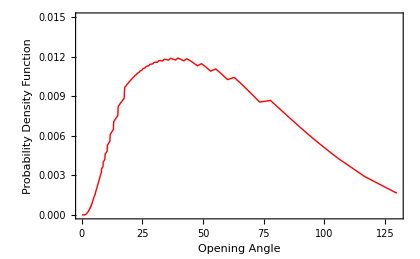

```mathematica
Plot[intOA[ang],{ang,0,130},FrameLabel->{"Opening Angle","Probability Density Function"},PlotRange -> {0,0.015},Frame->True,LabelStyle->{Black,15},ImageSize->420,PlotStyle->Directive[Red,Thick]]
```

### Convert To Histograms

```mathematica
testpts = 1000;
divisions = 130;
```

```mathematica
Clear[OAMCHits]
TotalTests = testpts*divisions
OAMCHits= ConstantArray[0,TotalTests/testpts];
divisionsList = ConstantArray[0,divisions];
```

130000

```mathematica
For[k=1,k≤divisions,k++,
OAMCDist=RandomReal[{0,1},{testpts,2}];
For[j=1,j≤testpts,j++,
n=OAMCDist[[j,1]]*(130/divisions)+k*(130/divisions);(*Gives opening angle for out trial*)
If[OAMCDist[[j,2]]*0.015< intOA[n],OAMCHits[[k]]++;divisionsList[[k]]=(k+0.5)*(130/divisions)]
]
]
OAMCHits
```

{4,14,44,72,87,157,170,257,302,318,386,439,484,522,533,581,586,658,677,676,688,725,733,728,733,746,747,783,769,763,765,777,785,792,785,775,785,795,766,793,776,785,779,790,758,769,737,762,768,768,741,729,725,738,726,703,693,706,696,685,691,675,714,715,648,653,646,639,636,619,624,570,556,599,557,571,583,546,561,554,532,510,529,536,491,480,458,477,468,455,419,416,410,363,382,365,364,361,384,323,319,313,308,316,273,302,269,253,231,263,224,225,209,240,206,199,161,191,171,172,171,169,164,138,130,161,117,134,126,100}

```mathematica
val=divisionsList;
freq=OAMCHits;
l=Length[val];
w=130/divisions;(*bin width*)
data=Flatten@Array[Table[val[[#]],{freq[[#]]}]&,l];
```

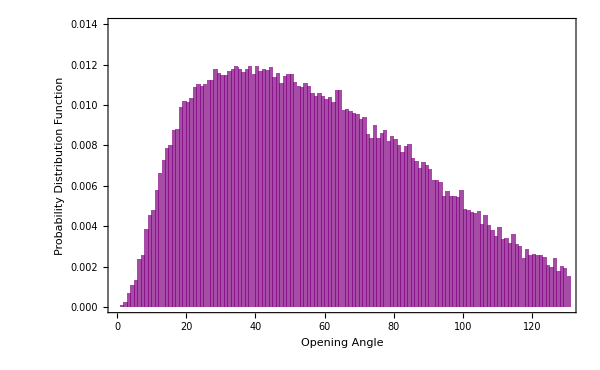

```mathematica
Histogram[data,{w},0.015/testpts #2&,Frame->True,LabelStyle->{Black,15},ChartStyle->Opacity[.7,Purple],ImageSize->600,PlotRange ->{{0,130},{0,0.014}},FrameLabel->{"Opening Angle","Probability Distribution Function"}]
```

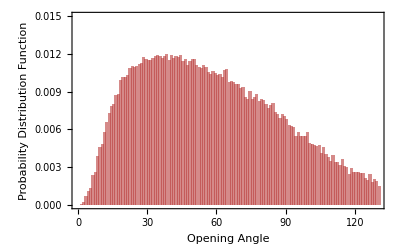

```mathematica
Histogram[data,{w},0.015/testpts #2&,Frame->True,LabelStyle->{Black,14,FontFamily->"Times"},ChartStyle->Opacity[.6,ColorData["DarkRainbow",1.0]],ImageSize->400,LabelStyle->{Black,14,FontFamily->"Times"},PlotRange ->{{0,130},{0,0.015}},FrameLabel->{"Opening Angle","Probability Distribution Function"}]
```

```mathematica
ColorData["DarkRainbow",1.0]
```

RGBColor[0.72987, 0.239399, 0.230961]